# Test eikonal approximation - square well

## Input is complex potential depth V (fm^-2), extension R (fm), wave number k(1/fm) Output is scattering amplitude f (k, theta), and cross section

## From Varner 1991 Phys Rep 201, 57 (1991)

First step - Partial wave

```mathematica
V=-1.9- .38 I; R=1.3 (12)^.33333-.225
```

2.75123

```mathematica
Clear[R]
```

```mathematica
R
```

3

```mathematica
j[l_,x_]:=SphericalBesselJ[l,x];n[l_,x_]:=SphericalBesselY[l,x]
```

```mathematica
jp[l_,y_]:=D[j[l,x],x]/.x->y;np[l_,y_]:=D[n[l,x],x]/.x->y
```

```mathematica
K[V_,k_]:=(k^2 -V)^(1/2);X[V_,k_,R_]:=R K[V,k]
```

```mathematica
Psi[l_,V_,k_,R_]:=j[l,X[V,k,R]]
                                                                                                                                                                                                                                                                                          K[V,1]
```

1.70657+0.111334 ⅈ

```mathematica
PsiP[l_,V_,k_,R__]:=+K [V,k]jp[l,X[V,k,R]]
```

```mathematica
gamma[l_,V_,k_,R_]:=PsiP[l,V,k,R]/Psi[l,V,k,R]
```

```mathematica
TanDelta[l_,V_,k_,R_]:=(gamma[l,V,k,R] j[l,k R]-k jp[l,k R])/(gamma[l,V,k,R] n[l,k R]-k np[l,k R])
```

```mathematica
TD0[V_,k_,R_]:=(-K[V,k]Cot[K[V,k]R]Sin[k R]+k Cos[k R])/(K[V,k] Cot[K[V,k]R]Cos[k R]+k Sin[k R])
```

```mathematica
TD0[V,3.,3.]
```

1.11409+0.357189 ⅈ

```mathematica
TD0[V,3.,3.]
```

1.11409+0.357189 ⅈ

```mathematica
Table[TanDelta[l,V,3.,3.],{l,0,20}]
```

{1.11409+0.357189 ⅈ,1.25227+0.501664 ⅈ,1.02033+0.32541 ⅈ,1.16318+0.385611 ⅈ,0.939519+0.329808 ⅈ,0.803768+0.201343 ⅈ,0.879987+0.233548 ⅈ,0.670267+0.217759 ⅈ,0.276923+0.0860427 ⅈ,0.0757166+0.0203131 ⅈ,0.0162641+0.00391918 ⅈ,0.00287982+0.000653111 ⅈ,0.000425418+0.0000932591 ⅈ,0.0000529673+0.0000113742 ⅈ,5.62369×10^-6+1.19117×10^-6 ⅈ,5.15081×10^-7+1.0804×10^-7 ⅈ,4.11274×10^-8+8.56394×10^-9 ⅈ,2.88946×10^-9+5.98294×10^-10 ⅈ,1.80083×10^-10+3.71223×10^-11 ⅈ,1.00281×10^-11+2.05975×10^-12 ⅈ,5.02128×10^-13+1.02831×10^-13 ⅈ}

```mathematica
Table[TanDelta[l,V,3.,3.],{l,0,20}]
```

{1.11409+0.357189 ⅈ,1.25227+0.501664 ⅈ,1.02033+0.32541 ⅈ,1.16318+0.385611 ⅈ,0.939519+0.329808 ⅈ,0.803768+0.201343 ⅈ,0.879987+0.233548 ⅈ,0.670267+0.217759 ⅈ,0.276923+0.0860427 ⅈ,0.0757166+0.0203131 ⅈ,0.0162641+0.00391918 ⅈ,0.00287982+0.000653111 ⅈ,0.000425418+0.0000932591 ⅈ,0.0000529673+0.0000113742 ⅈ,5.62369×10^-6+1.19117×10^-6 ⅈ,5.15081×10^-7+1.0804×10^-7 ⅈ,4.11274×10^-8+8.56394×10^-9 ⅈ,2.88946×10^-9+5.98294×10^-10 ⅈ,1.80083×10^-10+3.71223×10^-11 ⅈ,1.00281×10^-11+2.05975×10^-12 ⅈ,5.02128×10^-13+1.02831×10^-13 ⅈ}

```mathematica
Table[{l,TanDelta[l,V,5.,3.]},{l,0,30}]
```

{{0,0.625314+0.149069 ⅈ},{1,0.607209+0.15461 ⅈ},{2,0.606494+0.142577 ⅈ},{3,0.607651+0.154396 ⅈ},{4,0.563772+0.131372 ⅈ},{5,0.595903+0.144476 ⅈ},{6,0.528149+0.12829 ⅈ},{7,0.52062+0.115659 ⅈ},{8,0.528477+0.125876 ⅈ},{9,0.442237+0.104749 ⅈ},{10,0.405246+0.0852017 ⅈ},{11,0.42267+0.0898569 ⅈ},{12,0.373864+0.0884328 ⅈ},{13,0.23717+0.0593116 ⅈ},{14,0.108558+0.0265093 ⅈ},{15,0.0387808+0.0089926 ⅈ},{16,0.0114718+0.00254599 ⅈ},{17,0.00289065+0.000623158 ⅈ},{18,0.000629253+0.000133214 ⅈ},{19,0.000119538+0.0000250132 ⅈ},{20,0.000019997+4.15119×10^-6 ⅈ},{21,2.97049×10^-6+6.13097×10^-7 ⅈ},{22,3.94783×10^-7+8.11256×10^-8 ⅈ},{23,4.72565×10^-8+9.67766×10^-9 ⅈ},{24,5.12524×10^-9+1.04671×10^-9 ⅈ},{25,5.063×10^-10+1.03166×10^-10 ⅈ},{26,4.57711×10^-11+9.30895×10^-12 ⅈ},{27,3.8028×10^-12+7.72186×10^-13 ⅈ},{28,2.91478×10^-13+5.91063×10^-14 ⅈ},{29,2.06826×10^-14+4.18914×10^-15 ⅈ},{30,1.36295×10^-15+2.75776×10^-16 ⅈ}}

```mathematica
f[V_,k_,R_,theta_,Lmax_]:=1/k Sum[(2l+1)TanDelta[l,V,k,R]/(1-I TanDelta[l,V,k,R])LegendreP[l,Cos[theta]],{l,0,Lmax}]
```

```mathematica
Table[f[V,3,3.,t Pi/36,20],{t,0,36}]
```

{9.60054+10.8866 ⅈ,8.87411+10.2151 ⅈ,6.91782+8.37563 ⅈ,4.31222+5.83358 ⅈ,1.77092+3.19058 ⅈ,-0.11822+0.994886 ⅈ,-1.07552-0.413079 ⅈ,-1.16945-0.968843 ⅈ,-0.718287-0.85215 ⅈ,-0.117332-0.380858 ⅈ,0.323694+0.120263 ⅈ,0.469362+0.425392 ⅈ,0.355078+0.456073 ⅈ,0.116638+0.267292 ⅈ,-0.0998556-0.00999706 ⅈ,-0.204605-0.239243 ⅈ,-0.185999-0.333063 ⅈ,-0.0916901-0.276079 ⅈ,0.0108001-0.11504 ⅈ,0.0707058+0.0723307 ⅈ,0.0725329+0.213125 ⅈ,0.0334158+0.265239 ⅈ,-0.0136656+0.226151 ⅈ,-0.0395501+0.125219 ⅈ,-0.0319299+0.00615903 ⅈ,0.00241654-0.0915592 ⅈ,0.0446374-0.145378 ⅈ,0.0748785-0.153252 ⅈ,0.0816466-0.129145 ⅈ,0.0656749-0.0941097 ⅈ,0.0376264-0.0672353 ⅈ,0.0117241-0.0596537 ⅈ,-0.00123687-0.0727711 ⅈ,0.00166501-0.100091 ⅈ,0.0151957-0.130979 ⅈ,0.0294954-0.154688 ⅈ,0.0354753-0.163515 ⅈ}

```mathematica
Table[f[V,3,3.,t Pi/36,20],{t,0,36}]
```

{9.60054+10.8866 ⅈ,8.87411+10.2151 ⅈ,6.91782+8.37563 ⅈ,4.31222+5.83358 ⅈ,1.77092+3.19058 ⅈ,-0.11822+0.994886 ⅈ,-1.07552-0.413079 ⅈ,-1.16945-0.968843 ⅈ,-0.718287-0.85215 ⅈ,-0.117332-0.380858 ⅈ,0.323694+0.120263 ⅈ,0.469362+0.425392 ⅈ,0.355078+0.456073 ⅈ,0.116638+0.267292 ⅈ,-0.0998556-0.00999706 ⅈ,-0.204605-0.239243 ⅈ,-0.185999-0.333063 ⅈ,-0.0916901-0.276079 ⅈ,0.0108001-0.11504 ⅈ,0.0707058+0.0723307 ⅈ,0.0725329+0.213125 ⅈ,0.0334158+0.265239 ⅈ,-0.0136656+0.226151 ⅈ,-0.0395501+0.125219 ⅈ,-0.0319299+0.00615903 ⅈ,0.00241654-0.0915592 ⅈ,0.0446374-0.145378 ⅈ,0.0748785-0.153252 ⅈ,0.0816466-0.129145 ⅈ,0.0656749-0.0941097 ⅈ,0.0376264-0.0672353 ⅈ,0.0117241-0.0596537 ⅈ,-0.00123687-0.0727711 ⅈ,0.00166501-0.100091 ⅈ,0.0151957-0.130979 ⅈ,0.0294954-0.154688 ⅈ,0.0354753-0.163515 ⅈ}

```mathematica
Table[f[V,3,3.,t Pi/20,15],{t,0,20}]
```

{9.60054+10.8866 ⅈ,7.3832+8.81777 ⅈ,2.73658+4.22149 ⅈ,-0.616414+0.327279 ⅈ,-1.11011-0.990286 ⅈ,-0.117332-0.380858 ⅈ,0.464176+0.385987 ⅈ,0.216829+0.361624 ⅈ,-0.157517-0.113867 ⅈ,-0.17105-0.332973 ⅈ,0.0108-0.11504 ⅈ,0.0763501+0.191282 ⅈ,0.00397171+0.251386 ⅈ,-0.0405287+0.0772897 ⅈ,0.010923-0.106187 ⅈ,0.0748784-0.153252 ⅈ,0.0702751-0.100986 ⅈ,0.0209902-0.0600713 ⅈ,-0.00184582-0.0825428 ⅈ,0.0183314-0.136602 ⅈ,0.0354749-0.163515 ⅈ}

```mathematica
Table[Feik[V,3,3.,t Pi/36],{t,0,36}]
```

{8.92585+10.3694 ⅈ,8.29483+9.77655 ⅈ,6.58141+8.1465 ⅈ,4.25788+5.87415 ⅈ,1.91857+3.47046 ⅈ,0.0785536+1.40437 ⅈ,-0.977137-0.0232869 ⅈ,-1.24223-0.73327 ⅈ,-0.933029-0.841656 ⅈ,-0.367633-0.578249 ⅈ,0.161376-0.189681 ⅈ,0.472663+0.136192 ⅈ,0.520213+0.30511 ⅈ,0.364499+0.310975 ⅈ,0.116928+0.204815 ⅈ,-0.114436+0.0569945 ⅈ,-0.259518-0.0725986 ⅈ,-0.296247-0.149697 ⅈ,-0.241469-0.166906 ⅈ,-0.132839-0.136151 ⅈ,-0.0109671-0.0782554 ⅈ,0.0926825-0.0140084 ⅈ,0.160736+0.0411992 ⅈ,0.189136+0.0791336 ⅈ,0.183227+0.0979133 ⅈ,0.153073+0.0999718 ⅈ,0.109575+0.089861 ⅈ,0.0620011+0.0725144 ⅈ,0.0169049+0.0521796 ⅈ,-0.0219344+0.031959 ⅈ,-0.0530097+0.0137788 ⅈ,-0.0763761-0.00140556 ⅈ,-0.0929736-0.0133205 ⅈ,-0.104091-0.0220935 ⅈ,-0.110994-0.0280267 ⅈ,-0.114703-0.0314351 ⅈ,-0.115866-0.0325443 ⅈ}

```mathematica
Table[Feik[V,3,3.,t Pi/36],{t,0,36}]
```

{8.92585+10.3694 ⅈ,8.29483+9.77655 ⅈ,6.58141+8.1465 ⅈ,4.25788+5.87415 ⅈ,1.91857+3.47046 ⅈ,0.0785536+1.40437 ⅈ,-0.977137-0.0232869 ⅈ,-1.24223-0.73327 ⅈ,-0.933029-0.841656 ⅈ,-0.367633-0.578249 ⅈ,0.161376-0.189681 ⅈ,0.472663+0.136192 ⅈ,0.520213+0.30511 ⅈ,0.364499+0.310975 ⅈ,0.116928+0.204815 ⅈ,-0.114436+0.0569945 ⅈ,-0.259518-0.0725986 ⅈ,-0.296247-0.149697 ⅈ,-0.241469-0.166906 ⅈ,-0.132839-0.136151 ⅈ,-0.0109671-0.0782554 ⅈ,0.0926825-0.0140084 ⅈ,0.160736+0.0411992 ⅈ,0.189136+0.0791336 ⅈ,0.183227+0.0979133 ⅈ,0.153073+0.0999718 ⅈ,0.109575+0.089861 ⅈ,0.0620011+0.0725144 ⅈ,0.0169049+0.0521796 ⅈ,-0.0219344+0.031959 ⅈ,-0.0530097+0.0137788 ⅈ,-0.0763761-0.00140556 ⅈ,-0.0929736-0.0133205 ⅈ,-0.104091-0.0220935 ⅈ,-0.110994-0.0280267 ⅈ,-0.114703-0.0314351 ⅈ,-0.115866-0.0325443 ⅈ}

```mathematica
Table[Feik[V,3,3.,t Pi/20],{t,0,20}]
```

{8.92585+10.3694 ⅈ,6.99106+8.53919 ⅈ,2.81929+4.415 ⅈ,-0.444265+0.747237 ⅈ,-1.21675-0.796733 ⅈ,-0.367633-0.578249 ⅈ,0.431869+0.0819632 ⅈ,0.444491+0.325757 ⅈ,0.0174446+0.146862 ⅈ,-0.275451-0.0928113 ⅈ,-0.241469-0.166906 ⅈ,-0.0346989-0.0909526 ⅈ,0.138307+0.0208875 ⅈ,0.190384+0.0888796 ⅈ,0.14511+0.098762 ⅈ,0.0620011+0.0725144 ⅈ,-0.0147666+0.0358858 ⅈ,-0.0679072+0.00427938 ⅈ,-0.0980037-0.0171917 ⅈ,-0.111965-0.0289014 ⅈ,-0.115866-0.0325443 ⅈ}

```mathematica
Table[f[V,4,3.,t Pi/20,15],{t,0,2}]
```

{11.6998+9.85332 ⅈ,7.54666+6.83946 ⅈ,0.758527+1.50062 ⅈ}

```mathematica
Table[Feik[V,4,3.,t Pi/20],{t,0,2}]
```

{11.2791+9.59508 ⅈ,7.42464+6.79222 ⅈ,0.930633+1.731 ⅈ}

```mathematica
Table[f[V,5,3.,t Pi/20,15],{t,0,2}]
```

{12.8518+8.94958 ⅈ,6.56316+5.04877 ⅈ,-0.862237-0.0599113 ⅈ}

```mathematica
Table[Feik[V,5,3.,t Pi/20],{t,0,2}]
```

{12.6703+8.8197 ⅈ,6.55634+5.07694 ⅈ,-0.77538+0.0806419 ⅈ}

```mathematica
Table[f[V,6,3.,t Pi/20,15],{t,0,2}]
```

{12.2022+7.71245 ⅈ,5.22707+3.58849 ⅈ,-1.30203-0.557176 ⅈ}

```mathematica
Table[Feik[V,6,3.,t Pi/20],{t,0,2}]
```

{13.5627+8.16973 ⅈ,5.06467+3.57191 ⅈ,-1.36318-0.539375 ⅈ}

Second step - Eikonal

```mathematica
Feik[V_,k_,R_,theta_]:=k/I NIntegrate[ b BesselJ[0,2k Sin[theta/2]b](Exp[-I V/k Sqrt[R^2-b^2]]-1),{b,0,R}]
```

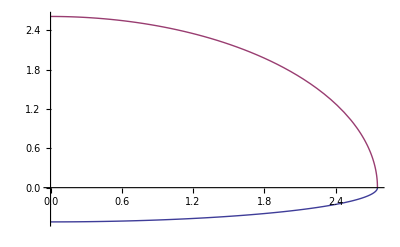

```mathematica
k=2;Plot[{Re[(-I V/k Sqrt[R^2-b^2])],Im[-I V/k Sqrt[R^2-b^2]]},{b,0,R}]
```

```mathematica
kk
```

0

```mathematica
ClearAll[kk]
```

```mathematica
Assuming[{kk∈Reals,RR∈Reals,kk>0,RR>0},Integrate[ b  (Exp[-I VV/kk Sqrt[RR^2-b^2]]-1),{b,0,RR}]]
```

-RR^2/2+(kk (-kk+ⅇ^(-(ⅈ RR VV)/kk) (kk+ⅈ RR VV)))/VV^2

```mathematica
aws=0.54
```

0.54

```mathematica
FeikWS[V_,k_,R_,theta_]:=k/I NIntegrate[ b BesselJ[0,2k Sin[theta/2]b](Exp[-I V/2/k Tb[b,R,aws]]-1),{b,0,15}]
```

```mathematica
FeikWS[V,3,3,0]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3 + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

14.1432+12.2368 ⅈ

```mathematica
FeikWS[V,3,3,0]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3 + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

12.5172+22.9076 ⅈ

```mathematica
Table[FeikWS[V,k,3,0],{k,3,7}]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3 + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{12.5172+22.9076 ⅈ,19.27+25.1682 ⅈ,24.488+25.2254 ⅈ,28.2863+24.4736 ⅈ,31.07+23.4857 ⅈ}

```mathematica
Table[FeikWS[V,k,3,0],{k,3,7}]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3 + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{12.5172+22.9076 ⅈ,19.27+25.1682 ⅈ,24.488+25.2254 ⅈ,28.2863+24.4736 ⅈ,31.07+23.4857 ⅈ}

```mathematica
Table[FeikWS[V,k,1,5j],{j,0,36}]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-1 + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{1.78357+1.25181 ⅈ,0.443065+0.62355 ⅈ,-0.0112327+0.236586 ⅈ,0.000140401+0.252999 ⅈ,0.568986+0.698579 ⅈ,1.75332+1.24008 ⅈ,0.33796+0.555214 ⅈ,-0.0193609+0.224015 ⅈ,0.0156199+0.273635 ⅈ,0.715885+0.77922 ⅈ,1.66631+1.20598 ⅈ,0.252122+0.494059 ⅈ,-0.0248821+0.214978 ⅈ,0.0363262+0.298945 ⅈ,0.881742+0.863646 ⅈ,1.5328+1.15246 ⅈ,0.18327+0.440144 ⅈ,-0.0282412+0.209245 ⅈ,0.063673+0.329436 ⅈ,1.06154+0.949148 ⅈ,1.36721+1.08384 ⅈ,0.128871+0.393233 ⅈ,-0.0297139+0.206669 ⅈ,0.0993939+0.365644 ⅈ,1.24667+1.0321 ⅈ,1.18508+1.005 ⅈ,0.0864415+0.352911 ⅈ,-0.0294222+0.207182 ⅈ,0.145547+0.408108 ⅈ,1.42498+1.10808 ⅈ,1.00054+0.920746 ⅈ,0.0537236+0.318668 ⅈ,-0.0273419+0.210799 ⅈ,0.204478+0.457313 ⅈ,1.58161+1.1722 ⅈ,0.824616+0.835245 ⅈ,0.0287658+0.289963 ⅈ}

```mathematica
R
```

3.

```mathematica
aws
```

0.54

```mathematica
aws
```

0.54

```mathematica
Tb[b_,R_,aws_]:=NIntegrate[1/(1+Exp[(Sqrt[b^2+z^2]-R)/aws]),{z,-15,15}]
```

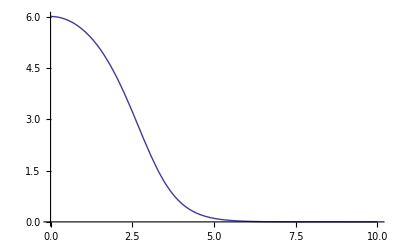

```mathematica
Plot[Tb[b,3,aws],{b,0,10}]
```

```mathematica
Plot[Tb[b,3,aws],{b,0,10}]
```

-Graphics-

```mathematica
Clear[R,aws];D[1/(1+Exp[(Sqrt[b^2+z^2]-R)/aws]),b]
```

-(b ⅇ^((-R+√(b^2+z^2))/aws))/(aws (1+ⅇ^((-R+√(b^2+z^2))/aws))^2 √(b^2+z^2))

```mathematica
Tbp[b_,R_,aws_]:= NIntegrate[ -(b ⅇ^((-R+√(b^2+z^2))/aws))/(aws (1+ⅇ^((-R+√(b^2+z^2))/aws))^2 √(b^2+z^2)),{z,-15,15}]
```

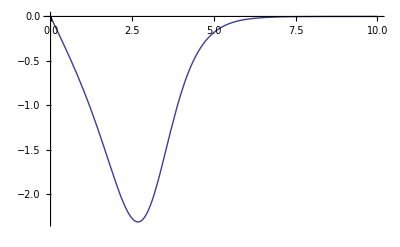

```mathematica
Plot[Tbp[b,3,aws],{b,0,10}]
```

```mathematica
R=3.;aws=.54
```

0.54

```mathematica
Tbp[1.,R,aws]
```

-0.820736

```mathematica
Simplify[D[1/(1+Exp[(Sqrt[b^2+z^2]-R)/aws])^2,b]]
```

-(247817. b ⅇ^(1.85185 √(b^2+z^2)))/((258.671+ⅇ^(1.85185 √(b^2+z^2)))^3 √(b^2+z^2))

```mathematica
Clear[R,aws];FullSimplify[1/(1+Exp[(Sqrt[b^2+z^2]-R)/aws])^2+b D[1/(1+Exp[(Sqrt[b^2+z^2]-R)/aws])^2,b]]
```

(1+ⅇ^((-R+√(b^2+z^2))/aws) (1-(2 b^2)/(aws √(b^2+z^2))))/((1+ⅇ^((-R+√(b^2+z^2))/aws))^3)

```mathematica
R=3.;aws=0.54
```

0.54

```mathematica
Tb1[b_,R_,aws_]:=NIntegrate[ (1+ⅇ^((-R+√(b^2+z^2))/aws) (1-(2 b^2)/(aws √(b^2+z^2))))/((1+ⅇ^((-R+√(b^2+z^2))/aws))^3) ,{z,-15,15}]
```

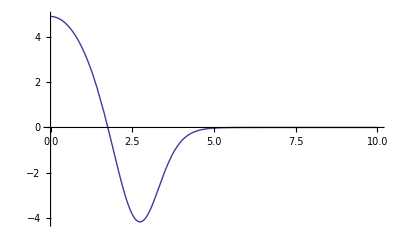

```mathematica
Plot[Tb1[b,R,aws],{b,0,10},PlotRange->All]
```

```mathematica
Clear[R,aws];FullSimplify[D[1/(1+Exp[(Sqrt[b^2+z^2]-R)/aws]),{b,2}]]
```

-((aws z^2)/((b^2+z^2)^(3/2))+(b^2 Tanh[(R-√(b^2+z^2))/(2 aws)])/(b^2+z^2))/(2 aws^2 (1+Cosh[(R-√(b^2+z^2))/aws]))

```mathematica
Tbpp[b_,R_,aws_]:= NIntegrate[-((aws z^2)/((b^2+z^2)^(3/2))+(b^2 Tanh[(R-√(b^2+z^2))/(2 aws)])/(b^2+z^2))/(2 aws^2 (1+Cosh[(R-√(b^2+z^2))/aws]))  ,{z,-15,15}]
```

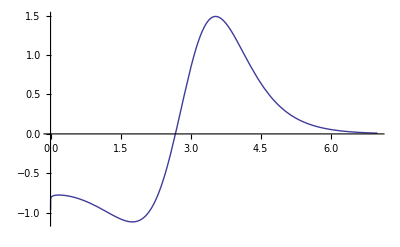

```mathematica
R=3.;aws=0.54;Plot[Tbpp[b,R,aws],{b,0,7}]
```

```mathematica
Re[2+3I]
```

2

```mathematica
k
```

3

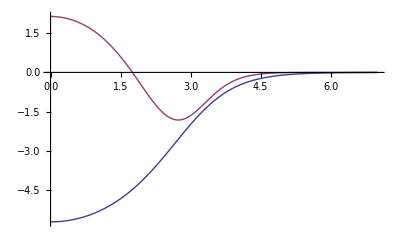

```mathematica
Plot[{Re[V/2/k Tb[b,R,aws]],Re[  V^2/8/k^3Tb1[b,R,aws]]},{b,0,7}]
```

```mathematica
w2[b_,R_,aws_]:=(V/2/k)^2/8 b Tbp[b,R,aws] (1/b Tbp[b,R,aws]+Tbpp[b,R,aws])
```

```mathematica
k
```

3

```mathematica
Tbp[1,R,aws]
```

-0.820736

```mathematica
w2[1,R,aws]
```

0.0172195+0.00717479 ⅈ

```mathematica
k
```

3

```mathematica
Table[w2[b+.0000001,R,aws],{b,0,7}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {2.77781×10^-7}. NIntegrate obtained -9.86476×10^-8 and 2.02762×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {2.77781×10^-7}. NIntegrate obtained -0.972268 and 0.000092304 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{2.32514×10^-16+9.6881×10^-17 ⅈ,0.0172195+0.00717479 ⅈ,0.0898877+0.0374532 ⅈ,-0.00853511-0.0035563 ⅈ,-0.0394249-0.016427 ⅈ,-0.00287032-0.00119597 ⅈ,-0.000115942-0.0000483091 ⅈ,-4.04563×10^-6-1.68568×10^-6 ⅈ}

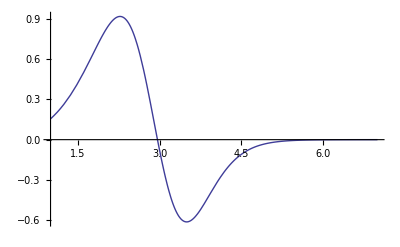

```mathematica
k=1;Plot[Re[w2[b,R,aws]],{b,1,7}]
```

```mathematica
Plot[{Re[V/2/k Tb[b,R,aws]],Re[  V^2/8/k^3Tb1[b,R,aws]]},{b,0,7}]
```

-Graphics-

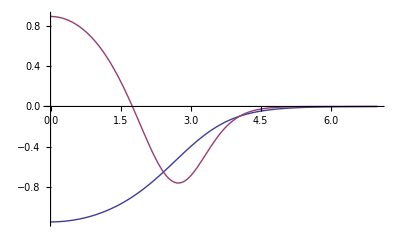

```mathematica
Plot[{Im[V/2/k Tb[b,R,aws]],Im[  V^2/8/k^3Tb1[b,R,aws]]},{b,0,7}]
```

```mathematica
k=1;Plot[{Re[V/2/k Tb[b,R,aws]],Re[  V^2/8/k^3Tb1[b,R,aws]]},{b,0,7}]
```

-Graphics-

```mathematica
Plot[{Im[V/2/k Tb[b,R,aws]],Im[  V^2/8/k^3Tb1[b,R,aws]]},{b,0,7}]
```

-Graphics-

```mathematica
First eikonal correction wallace PRL 27,622 eq 23
```

```mathematica
FeikWS1[V_,k_,R_,theta_]:=k/I NIntegrate[ b BesselJ[0,2k Sin[theta/2]b](Exp[-I V/2/k Tb[b,R,aws]-I  V^2/8/k^3Tb1[b,R,aws]]-1),{b,0,15}]
```

```mathematica
Table[{FeikWS[V,k,R,0],FeikWS1[V,k,R,0]},{k,1,3}]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3. + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{{3.22489+8.21064 ⅈ,1.61739+9.6372 ⅈ},{9.63498+12.5841 ⅈ,10.0328+13.877 ⅈ},{14.1432+12.2368 ⅈ,14.5428+12.7533 ⅈ}}

```mathematica
Table[{FeikWS[V,k,R,0],FeikWS1[V,k,R,0]},{k,1,3}]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3. + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{{3.22489+8.21064 ⅈ,1.61739+9.6372 ⅈ},{9.63498+12.5841 ⅈ,10.0328+13.877 ⅈ},{14.1432+12.2368 ⅈ,14.5428+12.7533 ⅈ}}

```mathematica
Get second correction
```

```mathematica
Clear[R,aws];FullSimplify[1/(1+Exp[(Sqrt[b^2+z^2]-R)/aws])^3+5/3b D[1/(1+Exp[(Sqrt[b^2+z^2]-R)/aws])^3,b]+ 1/3b^2D[1/(1+Exp[(Sqrt[b^2+z^2]-R)/aws])^3,{b,2}]]
```

(ⅇ^((3 R)/aws) (b^4 ⅇ^((√(b^2+z^2))/aws) (-ⅇ^(R/aws)+3 ⅇ^((√(b^2+z^2))/aws)) √(b^2+z^2)+aws^2 (ⅇ^(R/aws)+ⅇ^((√(b^2+z^2))/aws))^2 (b^2+z^2)^(3/2)-aws b^2 ⅇ^((√(b^2+z^2))/aws) (ⅇ^(R/aws)+ⅇ^((√(b^2+z^2))/aws)) (5 b^2+6 z^2)))/(aws^2 (ⅇ^(R/aws)+ⅇ^((√(b^2+z^2))/aws))^5 (b^2+z^2)^(3/2))

```mathematica
Tb2[b_,R_,aws_]:=NIntegrate[(ⅇ^((3 R)/aws) (b^4 ⅇ^((√(b^2+z^2))/aws) (-ⅇ^(R/aws)+3 ⅇ^((√(b^2+z^2))/aws)) √(b^2+z^2)+aws^2 (ⅇ^(R/aws)+ⅇ^((√(b^2+z^2))/aws))^2 (b^2+z^2)^(3/2)-aws b^2 ⅇ^((√(b^2+z^2))/aws) (ⅇ^(R/aws)+ⅇ^((√(b^2+z^2))/aws)) (5 b^2+6 z^2)))/(aws^2 (ⅇ^(R/aws)+ⅇ^((√(b^2+z^2))/aws))^5 (b^2+z^2)^(3/2)) ,{z,-15,15}]
```

```mathematica
Clear[R,aws];FullSimplify[2b D[1/(1+Exp[(Sqrt[b^2+z^2]-R)/aws])^2,b]+b^2 D[1/(1+Exp[(Sqrt[b^2+z^2]-R)/aws])^2,{b,2}]]
```

-(2 b^2 ⅇ^((2 R+√(b^2+z^2))/aws) (b^2 (ⅇ^(R/aws)-2 ⅇ^((√(b^2+z^2))/aws)) √(b^2+z^2)+aws (ⅇ^(R/aws)+ⅇ^((√(b^2+z^2))/aws)) (2 b^2+3 z^2)))/(aws^2 (ⅇ^(R/aws)+ⅇ^((√(b^2+z^2))/aws))^4 (b^2+z^2)^(3/2))

```mathematica
tau1p[b_,R_,aws_]:=-NIntegrate[-(2 b^2 ⅇ^((2 R+√(b^2+z^2))/aws) (b^2 (ⅇ^(R/aws)-2 ⅇ^((√(b^2+z^2))/aws)) √(b^2+z^2)+aws (ⅇ^(R/aws)+ⅇ^((√(b^2+z^2))/aws)) (2 b^2+3 z^2)))/(aws^2 (ⅇ^(R/aws)+ⅇ^((√(b^2+z^2))/aws))^4 (b^2+z^2)^(3/2)),{z,15,15}]
```

```mathematica
R=3;aws=0.54
```

0.54

```mathematica
FeikWS2[V_,k_,R_,theta_]:=k/I NIntegrate[ b BesselJ[0,2k Sin[theta/2]b](Exp[-I V/2/k Tb[b,R,aws]-I  V^2/8/k^3Tb1[b,R,aws]-I V^3/16/k^5 Tb2[b,R,aws]-I b V^2/k^2 Tbp[b,R,aws]^2/96-w2[b,R,aws]]-1),{b,0,15}]
```

## get third correction

```mathematica
Clear[R,aws];FullSimplify[5/4/(1+Exp[(Sqrt[b^2+z^2]-R)/aws])^4+11/4b D[1/(1+Exp[(Sqrt[b^2+z^2]-R)/aws])^4,b]+b^2 D[1/(1+Exp[(Sqrt[b^2+z^2]-R)/aws])^4,{b,2}]+b^3/12 D[1/(1+Exp[(Sqrt[b^2+z^2]-R)/aws])^4,{b,3}]]
```

(ⅇ^((4 R)/aws) (-4 b^6 ⅇ^((√(b^2+z^2))/aws) (ⅇ^((2 R)/aws)+16 ⅇ^((2 √(b^2+z^2))/aws)-13 ⅇ^((R+√(b^2+z^2))/aws)) (b^2+z^2)+15 aws^3 (ⅇ^(R/aws)+ⅇ^((√(b^2+z^2))/aws))^3 (b^2+z^2)^(5/2)+12 aws b^4 ⅇ^((√(b^2+z^2))/aws) (-ⅇ^((2 R)/aws)+4 ⅇ^((2 √(b^2+z^2))/aws)+3 ⅇ^((R+√(b^2+z^2))/aws)) √(b^2+z^2) (4 b^2+5 z^2)-12 aws^2 b^2 ⅇ^((√(b^2+z^2))/aws) (ⅇ^(R/aws)+ⅇ^((√(b^2+z^2))/aws))^2 (11 b^4+25 b^2 z^2+15 z^4)))/(12 aws^3 (ⅇ^(R/aws)+ⅇ^((√(b^2+z^2))/aws))^7 (b^2+z^2)^(5/2))

```mathematica
Tb3 is first term of wallace 17 without constant in front
```

```mathematica
Tb3[b_,R_,aws_]:=NIntegrate[(ⅇ^((4 R)/aws) (-4 b^6 ⅇ^((√(b^2+z^2))/aws) (ⅇ^((2 R)/aws)+16 ⅇ^((2 √(b^2+z^2))/aws)-13 ⅇ^((R+√(b^2+z^2))/aws)) (b^2+z^2)+15 aws^3 (ⅇ^(R/aws)+ⅇ^((√(b^2+z^2))/aws))^3 (b^2+z^2)^(5/2)+12 aws b^4 ⅇ^((√(b^2+z^2))/aws) (-ⅇ^((2 R)/aws)+4 ⅇ^((2 √(b^2+z^2))/aws)+3 ⅇ^((R+√(b^2+z^2))/aws)) √(b^2+z^2) (4 b^2+5 z^2)-12 aws^2 b^2 ⅇ^((√(b^2+z^2))/aws) (ⅇ^(R/aws)+ⅇ^((√(b^2+z^2))/aws))^2 (11 b^4+25 b^2 z^2+15 z^4)))/(12 aws^3 (ⅇ^(R/aws)+ⅇ^((√(b^2+z^2))/aws))^7 (b^2+z^2)^(5/2)) ,{z,-15,15}]
```

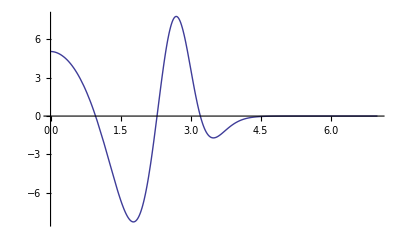

```mathematica
R=3;aws=.54;Plot[Tb3[b,R,aws],{b,0,7}]
```

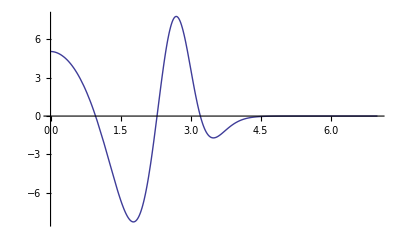

```mathematica
y1=Plot[Tb3f[b],{b,0,7}]
```

```mathematica
y2=%443
```

-Graphics-

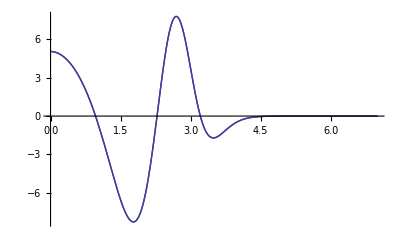

```mathematica
Show[y1,y2]
```

```mathematica
Tb3f[1]
```

-6.60263

```mathematica
tb3t=Table[{.05 j,Tb3[.05j,R,aws]},{j,0,300}]
```

{{0.,5.04578},{0.05,5.03189},{0.1,4.99182},{0.15,4.92628},{0.2,4.83541},{0.25,4.71907},{0.3,4.57699},{0.35,4.40873},{0.4,4.2138},{0.45,3.99161},{0.5,3.74154},{0.55,3.46296},{0.6,3.15522},{0.65,2.81775},{0.7,2.45004},{0.75,2.05171},{0.8,1.62256},{0.85,1.16267},{0.9,0.672392},{0.95,0.152521},{1.,-0.395662},{1.05,-0.97026},{1.1,-1.56865},{1.15,-2.18735},{1.2,-2.8219},{1.25,-3.46669},{1.3,-4.11487},{1.35,-4.75821},{1.4,-5.38698},{1.45,-5.98992},{1.5,-6.55423},{1.55,-7.0656},{1.6,-7.50837},{1.65,-7.8658},{1.7,-8.12048},{1.75,-8.25486},{1.8,-8.25197},{1.85,-8.09631},{1.9,-7.77492},{1.95,-7.27848},{2.,-6.60263},{2.05,-5.74917},{2.1,-4.72719},{2.15,-3.55398},{2.2,-2.25553},{2.25,-0.866479},{2.3,0.570511},{2.35,2.00621},{2.4,3.38703},{2.45,4.6579},{2.5,5.76575},{2.55,6.66326},{2.6,7.31258},{2.65,7.6885},{2.7,7.78089},{2.75,7.59584},{2.8,7.15545},{2.85,6.49607},{2.9,5.66535},{2.95,4.71816},{3.,3.71205},{3.05,2.70265},{3.1,1.73966},{3.15,0.86365},{3.2,0.104131},{3.25,-0.521127},{3.3,-1.00561},{3.35,-1.35262},{3.4,-1.57318},{3.45,-1.68371},{3.5,-1.70361},{3.55,-1.65324},{3.6,-1.55218},{3.65,-1.41804},{3.7,-1.26577},{3.75,-1.10731},{3.8,-0.951633},{3.85,-0.804998},{3.9,-0.671343},{3.95,-0.552728},{4.,-0.449789},{4.05,-0.36215},{4.1,-0.288768},{4.15,-0.228216},{4.2,-0.178898},{4.25,-0.139192},{4.3,-0.107557},{4.35,-0.0825881},{4.4,-0.0630484},{4.45,-0.0478748},{4.5,-0.0361745},{4.55,-0.0272099},{4.6,-0.0203815},{4.65,-0.015208},{4.7,-0.0113074},{4.75,-0.00837978},{4.8,-0.00619135},{4.85,-0.00456167},{4.9,-0.00335228},{4.95,-0.00245765},{5.,-0.00179778},{5.05,-0.0013124},{5.1,-0.000956252},{5.15,-0.000695527},{5.2,-0.000505063},{5.25,-0.000366201},{5.3,-0.000265143},{5.35,-0.000191721},{5.4,-0.000138462},{5.45,-0.0000998834},{5.5,-0.000071977},{5.55,-0.0000518157},{5.6,-0.000037267},{5.65,-0.0000267798},{5.7,-0.0000192279},{5.75,-0.0000137951},{5.8,-9.89007×10^-6},{5.85,-7.08562×10^-6},{5.9,-5.07313×10^-6},{5.95,-3.63002×10^-6},{6.,-2.59592×10^-6},{6.05,-1.85539×10^-6},{6.1,-1.32542×10^-6},{6.15,-9.4636×10^-7},{6.2,-6.75391×10^-7},{6.25,-4.81792×10^-7},{6.3,-3.4354×10^-7},{6.35,-2.4486×10^-7},{6.4,-1.74457×10^-7},{6.45,-1.24249×10^-7},{6.5,-8.84593×10^-8},{6.55,-6.29567×10^-8},{6.6,-4.47915×10^-8},{6.65,-3.18573×10^-8},{6.7,-2.2651×10^-8},{6.75,-1.61004×10^-8},{6.8,-1.14408×10^-8},{6.85,-8.1275×10^-9},{6.9,-5.77216×10^-9},{6.95,-4.09831×10^-9},{7.,-2.9091×10^-9},{7.05,-2.06445×10^-9},{7.1,-1.46469×10^-9},{7.15,-1.03892×10^-9},{7.2,-7.36751×10^-10},{7.25,-5.22348×10^-10},{7.3,-3.70258×10^-10},{7.35,-2.62395×10^-10},{7.4,-1.85915×10^-10},{7.45,-1.317×10^-10},{7.5,-9.32756×10^-11},{7.55,-6.60489×10^-11},{7.6,-4.67606×10^-11},{7.65,-3.30987×10^-11},{7.7,-2.34241×10^-11},{7.75,-1.65743×10^-11},{7.8,-1.17255×10^-11},{7.85,-8.2937×10^-12},{7.9,-5.86533×10^-12},{7.95,-4.14727×10^-12},{8.,-2.93197×10^-12},{8.05,-2.07246×10^-12},{8.1,-1.46468×10^-12},{8.15,-1.03498×10^-12},{8.2,-7.31225×10^-13},{8.25,-5.1654×10^-13},{8.3,-3.64831×10^-13},{8.35,-2.57641×10^-13},{8.4,-1.81917×10^-13},{8.45,-1.28431×10^-13},{8.5,-9.06573×10^-14},{8.55,-6.39846×10^-14},{8.6,-4.51531×10^-14},{8.65,-3.18596×10^-14},{8.7,-2.24768×10^-14},{8.75,-1.58552×10^-14},{8.8,-1.11828×10^-14},{8.85,-7.8863×10^-15},{8.9,-5.56084×10^-15},{8.95,-3.9206×10^-15},{9.,-2.76382×10^-15},{9.05,-1.94812×10^-15},{9.1,-1.37299×10^-15},{9.15,-9.67531×10^-16},{9.2,-6.8173×10^-16},{9.25,-4.80296×10^-16},{9.3,-3.38341×10^-16},{9.35,-2.38315×10^-16},{9.4,-1.67841×10^-16},{9.45,-1.18194×10^-16},{9.5,-8.32236×10^-17},{9.55,-5.85934×10^-17},{9.6,-4.12482×10^-17},{9.65,-2.90345×10^-17},{9.7,-2.04351×10^-17},{9.75,-1.43812×10^-17},{9.8,-1.01197×10^-17},{9.85,-7.12026×10^-18},{9.9,-5.00934×10^-18},{9.95,-3.52388×10^-18},{10.,-2.47867×10^-18},{10.05,-1.74331×10^-18},{10.1,-1.22599×10^-18},{10.15,-8.62104×10^-19},{10.2,-6.06164×10^-19},{10.25,-4.26167×10^-19},{10.3,-2.99591×10^-19},{10.35,-2.1059×10^-19},{10.4,-1.48016×10^-19},{10.45,-1.04025×10^-19},{10.5,-7.31023×10^-20},{10.55,-5.1367×10^-20},{10.6,-3.60911×10^-20},{10.65,-2.53559×10^-20},{10.7,-1.78123×10^-20},{10.75,-1.25119×10^-20},{10.8,-8.78802×10^-21},{10.85,-6.17195×10^-21},{10.9,-4.33429×10^-21},{10.95,-3.04354×10^-21},{11.,-2.137×10^-21},{11.05,-1.50036×10^-21},{11.1,-1.0533×10^-21},{11.15,-7.39388×10^-22},{11.2,-5.18992×10^-22},{11.25,-3.64263×10^-22},{11.3,-2.55645×10^-22},{11.35,-1.79401×10^-22},{11.4,-1.25887×10^-22},{11.45,-8.83297×10^-23},{11.5,-6.19725×10^-23},{11.55,-4.3477×10^-23},{11.6,-3.04992×10^-23},{11.65,-2.13938×10^-23},{11.7,-1.50056×10^-23},{11.75,-1.05243×10^-23},{11.8,-7.38071×10^-24},{11.85,-5.17577×10^-24},{11.9,-3.62929×10^-24},{11.95,-2.54472×10^-24},{12.,-1.78414×10^-24},{12.05,-1.2508×10^-24},{12.1,-8.76837×10^-25},{12.15,-6.14641×10^-25},{12.2,-4.3082×10^-25},{12.25,-3.01955×10^-25},{12.3,-2.11622×10^-25},{12.35,-1.48304×10^-25},{12.4,-1.03924×10^-25},{12.45,-7.28204×10^-26},{12.5,-5.10227×10^-26},{12.55,-3.57476×10^-26},{12.6,-2.5044×10^-26},{12.65,-1.75443×10^-26},{12.7,-1.22897×10^-26},{12.75,-8.60837×10^-27},{12.8,-6.02941×10^-27},{12.85,-4.22284×10^-27},{12.9,-2.95739×10^-27},{12.95,-2.07103×10^-27},{13.,-1.45025×10^-27},{13.05,-1.01548×10^-27},{13.1,-7.11013×10^-28},{13.15,-4.97805×10^-28},{13.2,-3.48511×10^-28},{13.25,-2.43978×10^-28},{13.3,-1.7079×10^-28},{13.35,-1.1955×10^-28},{13.4,-8.36783×10^-29},{13.45,-5.85672×10^-29},{13.5,-4.09895×10^-29},{13.55,-2.86859×10^-29},{13.6,-2.00744×10^-29},{13.65,-1.40473×10^-29},{13.7,-9.82929×10^-30},{13.75,-6.87748×10^-30},{13.8,-4.81188×10^-30},{13.85,-3.3665×10^-30},{13.9,-2.35516×10^-30},{13.95,-1.64756×10^-30},{14.,-1.1525×10^-30},{14.05,-8.0616×10^-31},{14.1,-5.63871×10^-31},{14.15,-3.94382×10^-31},{14.2,-2.75826×10^-31},{14.25,-1.929×10^-31},{14.3,-1.34899×10^-31},{14.35,-9.43332×10^-32},{14.4,-6.59631×10^-32},{14.45,-4.61231×10^-32},{14.5,-3.2249×10^-32},{14.55,-2.25472×10^-32},{14.6,-1.57635×10^-32},{14.65,-1.10202×10^-32},{14.7,-7.70392×10^-33},{14.75,-5.38534×10^-33},{14.8,-3.7644×10^-33},{14.85,-2.63123×10^-33},{14.9,-1.8391×10^-33},{14.95,-1.28538×10^-33},{15.,-8.98339×10^-34}}

```mathematica
Tb3f=Interpolation[tb3t]
```

InterpolatingFunction[{{0.,15.}},<>]

```mathematica
Tb[.1,R,aws]
```

6.00018

```mathematica
tbt=Table[{.05j,Tb[.05j,R,aws]},{j,0,300}]
```

{{0.,6.00417},{0.05,6.00316},{0.1,6.00018},{0.15,5.99525},{0.2,5.98839},{0.25,5.97958},{0.3,5.96883},{0.35,5.95614},{0.4,5.94148},{0.45,5.92485},{0.5,5.90623},{0.55,5.8856},{0.6,5.86294},{0.65,5.83823},{0.7,5.81145},{0.75,5.78256},{0.8,5.75153},{0.85,5.71834},{0.9,5.68296},{0.95,5.64534},{1.,5.60545},{1.05,5.56325},{1.1,5.51871},{1.15,5.47178},{1.2,5.42242},{1.25,5.3706},{1.3,5.31627},{1.35,5.25938},{1.4,5.19991},{1.45,5.13781},{1.5,5.07305},{1.55,5.00559},{1.6,4.9354},{1.65,4.86247},{1.7,4.78676},{1.75,4.70826},{1.8,4.62698},{1.85,4.54292},{1.9,4.45609},{1.95,4.36651},{2.,4.27424},{2.05,4.17932},{2.1,4.08182},{2.15,3.98184},{2.2,3.87948},{2.25,3.77488},{2.3,3.66817},{2.35,3.55954},{2.4,3.44918},{2.45,3.3373},{2.5,3.22413},{2.55,3.10994},{2.6,2.99499},{2.65,2.87959},{2.7,2.76404},{2.75,2.64865},{2.8,2.53375},{2.85,2.41967},{2.9,2.30673},{2.95,2.19526},{3.,2.08557},{3.05,1.97797},{3.1,1.87273},{3.15,1.77011},{3.2,1.67036},{3.25,1.57369},{3.3,1.48027},{3.35,1.39026},{3.4,1.30378},{3.45,1.22093},{3.5,1.14175},{3.55,1.06629},{3.6,0.994555},{3.65,0.926515},{3.7,0.862132},{3.75,0.801341},{3.8,0.744062},{3.85,0.690199},{3.9,0.63964},{3.95,0.592268},{4.,0.547955},{4.05,0.506567},{4.1,0.467968},{4.15,0.432019},{4.2,0.39858},{4.25,0.367514},{4.3,0.338684},{4.35,0.311957},{4.4,0.287202},{4.45,0.264296},{4.5,0.243116},{4.55,0.223549},{4.6,0.205484},{4.65,0.188817},{4.7,0.173448},{4.75,0.159286},{4.8,0.146241},{4.85,0.134232},{4.9,0.123181},{4.95,0.113016},{5.,0.10367},{5.05,0.0950788},{5.1,0.087185},{5.15,0.0799339},{5.2,0.0732751},{5.25,0.0671617},{5.3,0.0615504},{5.35,0.0564012},{5.4,0.0516769},{5.45,0.0473433},{5.5,0.0433689},{5.55,0.0397244},{5.6,0.036383},{5.65,0.0333199},{5.7,0.0305123},{5.75,0.0279393},{5.8,0.0255814},{5.85,0.023421},{5.9,0.0214418},{5.95,0.0196286},{6.,0.0179677},{6.05,0.0164465},{6.1,0.0150534},{6.15,0.0137775},{6.2,0.0126092},{6.25,0.0115395},{6.3,0.0105601},{6.35,0.00966337},{6.4,0.00884246},{6.45,0.00809099},{6.5,0.0074031},{6.55,0.00677346},{6.6,0.00619716},{6.65,0.0056697},{6.7,0.00518697},{6.75,0.00474519},{6.8,0.00434091},{6.85,0.00397096},{6.9,0.00363243},{6.95,0.00332267},{7.,0.00303924},{7.05,0.00277991},{7.1,0.00254265},{7.15,0.00232558},{7.2,0.00212698},{7.25,0.0019453},{7.3,0.0017791},{7.35,0.00162706},{7.4,0.00148797},{7.45,0.00136075},{7.5,0.00124438},{7.55,0.00113793},{7.6,0.00104057},{7.65,0.000951519},{7.7,0.000870071},{7.75,0.000795579},{7.8,0.00072745},{7.85,0.000665143},{7.9,0.00060816},{7.95,0.000556049},{8.,0.000508393},{8.05,0.000464814},{8.1,0.000424962},{8.15,0.00038852},{8.2,0.000355197},{8.25,0.000324726},{8.3,0.000296865},{8.35,0.000271389},{8.4,0.000248095},{8.45,0.000226797},{8.5,0.000207324},{8.55,0.00018952},{8.6,0.000173242},{8.65,0.00015836},{8.7,0.000144754},{8.75,0.000132315},{8.8,0.000120943},{8.85,0.000110546},{8.9,0.000101042},{8.95,0.000092354},{9.,0.0000844116},{9.05,0.0000771511},{9.1,0.0000705141},{9.15,0.0000644472},{9.2,0.0000589014},{9.25,0.0000538321},{9.3,0.0000491985},{9.35,0.0000449631},{9.4,0.0000410917},{9.45,0.0000375532},{9.5,0.000034319},{9.55,0.0000313629},{9.6,0.0000286611},{9.65,0.0000261917},{9.7,0.0000239347},{9.75,0.000021872},{9.8,0.0000199868},{9.85,0.0000182639},{9.9,0.0000166893},{9.95,0.0000152502},{10.,0.0000139351},{10.05,0.0000127333},{10.1,0.0000116349},{10.15,0.0000106312},{10.2,9.71398×10^-6},{10.25,8.87578×10^-6},{10.3,8.10982×10^-6},{10.35,7.40988×10^-6},{10.4,6.77027×10^-6},{10.45,6.18581×10^-6},{10.5,5.65175×10^-6},{10.55,5.16374×10^-6},{10.6,4.71782×10^-6},{10.65,4.31036×10^-6},{10.7,3.93805×10^-6},{10.75,3.59786×10^-6},{10.8,3.28703×10^-6},{10.85,3.00302×10^-6},{10.9,2.74353×10^-6},{10.95,2.50643×10^-6},{11.,2.2898×10^-6},{11.05,2.09187×10^-6},{11.1,1.91104×10^-6},{11.15,1.74582×10^-6},{11.2,1.59487×10^-6},{11.25,1.45695×10^-6},{11.3,1.33095×10^-6},{11.35,1.21584×10^-6},{11.4,1.11067×10^-6},{11.45,1.01459×10^-6},{11.5,9.26816×10^-7},{11.55,8.46626×10^-7},{11.6,7.73367×10^-7},{11.65,7.06441×10^-7},{11.7,6.45302×10^-7},{11.75,5.89448×10^-7},{11.8,5.38425×10^-7},{11.85,4.91814×10^-7},{11.9,4.49234×10^-7},{11.95,4.10337×10^-7},{12.,3.74805×10^-7},{12.05,3.42348×10^-7},{12.1,3.12698×10^-7},{12.15,2.85614×10^-7},{12.2,2.60874×10^-7},{12.25,2.38275×10^-7},{12.3,2.17632×10^-7},{12.35,1.98775×10^-7},{12.4,1.81552×10^-7},{12.45,1.65819×10^-7},{12.5,1.51448×10^-7},{12.55,1.38322×10^-7},{12.6,1.26333×10^-7},{12.65,1.15382×10^-7},{12.7,1.05379×10^-7},{12.75,9.62432×10^-8},{12.8,8.78986×10^-8},{12.85,8.02768×10^-8},{12.9,7.33155×10^-8},{12.95,6.69573×10^-8},{13.,6.11501×10^-8},{13.05,5.58462×10^-8},{13.1,5.10019×10^-8},{13.15,4.65776×10^-8},{13.2,4.25367×10^-8},{13.25,3.88462×10^-8},{13.3,3.54756×10^-8},{13.35,3.23973×10^-8},{13.4,2.95859×10^-8},{13.45,2.70182×10^-8},{13.5,2.46733×10^-8},{13.55,2.25317×10^-8},{13.6,2.05759×10^-8},{13.65,1.87897×10^-8},{13.7,1.71585×10^-8},{13.75,1.56688×10^-8},{13.8,1.43083×10^-8},{13.85,1.30659×10^-8},{13.9,1.19313×10^-8},{13.95,1.08951×10^-8},{14.,9.94891×10^-9},{14.05,9.0848×10^-9},{14.1,8.2957×10^-9},{14.15,7.57509×10^-9},{14.2,6.91704×10^-9},{14.25,6.31612×10^-9},{14.3,5.76737×10^-9},{14.35,5.26626×10^-9},{14.4,4.80867×10^-9},{14.45,4.39081×10^-9},{14.5,4.00924×10^-9},{14.55,3.66081×10^-9},{14.6,3.34264×10^-9},{14.65,3.0521×10^-9},{14.7,2.78681×10^-9},{14.75,2.54456×10^-9},{14.8,2.32335×10^-9},{14.85,2.12137×10^-9},{14.9,1.93693×10^-9},{14.95,1.76852×10^-9},{15.,1.61474×10^-9}}

```mathematica
tbtf=Interpolation[tbt]
```

InterpolatingFunction[{{0.,15.}},<>]

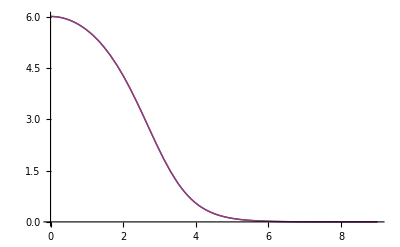

```mathematica
Plot[{tbtf[b],Tb[b,R,aws]},{b,0,9}]
```

```mathematica
tbtpt=Table[{.05j,Tbp[.05j,R,aws]},{j,0,300}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{0.,0.},{0.05,-0.0400136},{0.1,-0.0791065},{0.15,-0.117945},{0.2,-0.156708},{0.25,-0.195504},{0.3,-0.234413},{0.35,-0.273502},{0.4,-0.312831},{0.45,-0.352454},{0.5,-0.392422},{0.55,-0.432782},{0.6,-0.473581},{0.65,-0.514863},{0.7,-0.556671},{0.75,-0.599046},{0.8,-0.642027},{0.85,-0.685653},{0.9,-0.729958},{0.95,-0.774976},{1.,-0.820736},{1.05,-0.867264},{1.1,-0.914583},{1.15,-0.962709},{1.2,-1.01165},{1.25,-1.06142},{1.3,-1.11201},{1.35,-1.1634},{1.4,-1.21558},{1.45,-1.2685},{1.5,-1.32212},{1.55,-1.37637},{1.6,-1.43117},{1.65,-1.48641},{1.7,-1.54198},{1.75,-1.59773},{1.8,-1.65348},{1.85,-1.70904},{1.9,-1.76419},{1.95,-1.81866},{2.,-1.87218},{2.05,-1.92444},{2.1,-1.97509},{2.15,-2.02377},{2.2,-2.07008},{2.25,-2.11361},{2.3,-2.15394},{2.35,-2.19063},{2.4,-2.22323},{2.45,-2.25132},{2.5,-2.27447},{2.55,-2.2923},{2.6,-2.30445},{2.65,-2.3106},{2.7,-2.31051},{2.75,-2.30399},{2.8,-2.29093},{2.85,-2.27129},{2.9,-2.24513},{2.95,-2.21259},{3.,-2.1739},{3.05,-2.12937},{3.1,-2.07938},{3.15,-2.02439},{3.2,-1.9649},{3.25,-1.90148},{3.3,-1.83472},{3.35,-1.76522},{3.4,-1.69359},{3.45,-1.62045},{3.5,-1.54639},{3.55,-1.47195},{3.6,-1.39768},{3.65,-1.32405},{3.7,-1.25149},{3.75,-1.18039},{3.8,-1.11108},{3.85,-1.04384},{3.9,-0.978892},{3.95,-0.916421},{4.,-0.856561},{4.05,-0.799408},{4.1,-0.745016},{4.15,-0.693411},{4.2,-0.644586},{4.25,-0.598512},{4.3,-0.555137},{4.35,-0.514394},{4.4,-0.476202},{4.45,-0.440468},{4.5,-0.407091},{4.55,-0.375967},{4.6,-0.346985},{4.65,-0.320035},{4.7,-0.295006},{4.75,-0.271787},{4.8,-0.250271},{4.85,-0.230351},{4.9,-0.211926},{4.95,-0.194897},{5.,-0.179172},{5.05,-0.164659},{5.1,-0.151274},{5.15,-0.138937},{5.2,-0.127572},{5.25,-0.117108},{5.3,-0.107477},{5.35,-0.0986166},{5.4,-0.0904689},{5.45,-0.082979},{5.5,-0.0760961},{5.55,-0.069773},{5.6,-0.0639657},{5.65,-0.0586337},{5.7,-0.0537391},{5.75,-0.0492472},{5.8,-0.0451256},{5.85,-0.0413446},{5.9,-0.0378766},{5.95,-0.0346962},{6.,-0.0317801},{6.05,-0.0291067},{6.1,-0.026656},{6.15,-0.0244099},{6.2,-0.0223515},{6.25,-0.0204654},{6.3,-0.0187372},{6.35,-0.0171539},{6.4,-0.0157035},{6.45,-0.014375},{6.5,-0.0131582},{6.55,-0.0120438},{6.6,-0.0110233},{6.65,-0.0100887},{6.7,-0.00923304},{6.75,-0.00844956},{6.8,-0.00773226},{6.85,-0.00707558},{6.9,-0.00647443},{6.95,-0.00592414},{7.,-0.00542043},{7.05,-0.00495938},{7.1,-0.0045374},{7.15,-0.00415119},{7.2,-0.00379774},{7.25,-0.00347428},{7.3,-0.00317827},{7.35,-0.00290741},{7.4,-0.00265955},{7.45,-0.00243275},{7.5,-0.00222524},{7.55,-0.00203538},{7.6,-0.00186167},{7.65,-0.00170274},{7.7,-0.00155734},{7.75,-0.00142432},{7.8,-0.00130264},{7.85,-0.00119132},{7.9,-0.00108949},{7.95,-0.000996344},{8.,-0.000911141},{8.05,-0.000833206},{8.1,-0.000761922},{8.15,-0.000696722},{8.2,-0.000637089},{8.25,-0.000582548},{8.3,-0.000532665},{8.35,-0.000487045},{8.4,-0.000445323},{8.45,-0.000407168},{8.5,-0.000372275},{8.55,-0.000340366},{8.6,-0.000311186},{8.65,-0.000284503},{8.7,-0.000260103},{8.75,-0.000237792},{8.8,-0.000217391},{8.85,-0.000198737},{8.9,-0.00018168},{8.95,-0.000166085},{9.,-0.000151826},{9.05,-0.000138789},{9.1,-0.000126869},{9.15,-0.000115971},{9.2,-0.000106008},{9.25,-0.0000968991},{9.3,-0.0000885716},{9.35,-0.0000809586},{9.4,-0.0000739988},{9.45,-0.0000676364},{9.5,-0.0000618201},{9.55,-0.0000565031},{9.6,-0.0000516428},{9.65,-0.0000471998},{9.7,-0.0000431385},{9.75,-0.0000394261},{9.8,-0.0000360327},{9.85,-0.000032931},{9.9,-0.0000300958},{9.95,-0.0000275044},{10.,-0.0000251358},{10.05,-0.0000229708},{10.1,-0.0000209921},{10.15,-0.0000191836},{10.2,-0.0000175306},{10.25,-0.0000160199},{10.3,-0.0000146392},{10.35,-0.0000133773},{10.4,-0.0000122241},{10.45,-0.0000111701},{10.5,-0.0000102069},{10.55,-9.32669×10^-6},{10.6,-8.52225×10^-6},{10.65,-7.7871×10^-6},{10.7,-7.1153×10^-6},{10.75,-6.50137×10^-6},{10.8,-5.94035×10^-6},{10.85,-5.42769×10^-6},{10.9,-4.95921×10^-6},{10.95,-4.53112×10^-6},{11.,-4.13994×10^-6},{11.05,-3.78249×10^-6},{11.1,-3.45587×10^-6},{11.15,-3.15742×10^-6},{11.2,-2.88471×10^-6},{11.25,-2.63553×10^-6},{11.3,-2.40785×10^-6},{11.35,-2.19982×10^-6},{11.4,-2.00974×10^-6},{11.45,-1.83607×10^-6},{11.5,-1.67739×10^-6},{11.55,-1.5324×10^-6},{11.6,-1.39994×10^-6},{11.65,-1.27891×10^-6},{11.7,-1.16834×10^-6},{11.75,-1.06732×10^-6},{11.8,-9.75017×10^-7},{11.85,-8.90693×10^-7},{11.9,-8.13654×10^-7},{11.95,-7.43272×10^-7},{12.,-6.78972×10^-7},{12.05,-6.20229×10^-7},{12.1,-5.66563×10^-7},{12.15,-5.17536×10^-7},{12.2,-4.72748×10^-7},{12.25,-4.31832×10^-7},{12.3,-3.94454×10^-7},{12.35,-3.60308×10^-7},{12.4,-3.29115×10^-7},{12.45,-3.0062×10^-7},{12.5,-2.7459×10^-7},{12.55,-2.50812×10^-7},{12.6,-2.29091×10^-7},{12.65,-2.0925×10^-7},{12.7,-1.91125×10^-7},{12.75,-1.74569×10^-7},{12.8,-1.59446×10^-7},{12.85,-1.45632×10^-7},{12.9,-1.33013×10^-7},{12.95,-1.21487×10^-7},{13.,-1.10959×10^-7},{13.05,-1.01343×10^-7},{13.1,-9.25592×10^-8},{13.15,-8.45362×10^-8},{13.2,-7.7208×10^-8},{13.25,-7.05146×10^-8},{13.3,-6.4401×10^-8},{13.35,-5.8817×10^-8},{13.4,-5.37168×10^-8},{13.45,-4.90585×10^-8},{13.5,-4.48038×10^-8},{13.55,-4.09179×10^-8},{13.6,-3.73687×10^-8},{13.65,-3.41272×10^-8},{13.7,-3.11666×10^-8},{13.75,-2.84626×10^-8},{13.8,-2.59931×10^-8},{13.85,-2.37377×10^-8},{13.9,-2.16778×10^-8},{13.95,-1.97966×10^-8},{14.,-1.80785×10^-8},{14.05,-1.65094×10^-8},{14.1,-1.50764×10^-8},{14.15,-1.37677×10^-8},{14.2,-1.25725×10^-8},{14.25,-1.1481×10^-8},{14.3,-1.04842×10^-8},{14.35,-9.57384×10^-9},{14.4,-8.7425×10^-9},{14.45,-7.98331×10^-9},{14.5,-7.28999×10^-9},{14.55,-6.65685×10^-9},{14.6,-6.07866×10^-9},{14.65,-5.55066×10^-9},{14.7,-5.06849×10^-9},{14.75,-4.62818×10^-9},{14.8,-4.22609×10^-9},{14.85,-3.85891×10^-9},{14.9,-3.52362×10^-9},{14.95,-3.21744×10^-9},{15.,-2.93785×10^-9}}

```mathematica
tbpf=Interpolation[tbtpt]
```

InterpolatingFunction[{{0.,15.}},<>]

```mathematica
ND[tbtf[b],b,0]
```

ND[InterpolatingFunction[{{0.,15.}},<>][b],b,0]

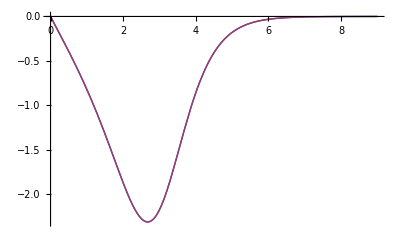

```mathematica
Plot[{tbpf[b],Tbp[b,R,aws]},{b,0,9}]
```

```mathematica
tpp[x_]:=(tbpf[x]-tbpf[0])/x
```

```mathematica
tpp[.001]
```

-0.813605

```mathematica
Series[tpp[x],{x,0,2}]
```

-0.813922+0.317412 x-0.888464 x^2+O[x]^3

```mathematica
-0.8139217894644672
```

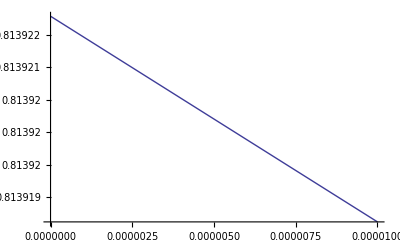

```mathematica
LogPlot[-tpp[x],{x,.000000001,.00001}]
```

```mathematica
Clear[R,aws];FullSimplify[D[1/(1+Exp[(Sqrt[b^2+z^2]-R)/aws]),{b,2}]]/.b->0
```

-1/(2 aws √(z^2) (1+Cosh[(R-√(z^2))/aws]))

```mathematica
Assuming[{eps∈Reals,aws∈Reals,R∈Reals,eps>0,aws>0,R>0,aws>eps,R>aws},Integrate[-1/(2 aws z (1+Cosh[(R-z)/aws])),{z,eps,Infinity}]]
```

∫_eps^∞ -1/(2 aws z (1+Cosh[(R-z)/aws]))ⅆz

```mathematica
tbtppt=Table[{.05j,Tbpp[.05j,R,aws]},{j,0,300}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {2.49672×10^-14}. NIntegrate obtained -6.10211 and 2.10944 for the integral and error estimates.

```mathematica
tbtppt={{0.,-0.8139217894644672},{0.05,-0.7865166317620055},{0.1,-0.7785040026892635},{0.15000000000000002,-0.775587482121676},{0.2,-0.775287353774411},{0.25,-0.7768053328231099},{0.30000000000000004,-0.7797754634550427},{0.35000000000000003,-0.7839967752251673},{0.4,-0.7893456577319615},{0.45,-0.795739582209907},{0.5,-0.8031195223317148},{0.55,-0.811440343209212},{0.6000000000000001,-0.8206649730122642},{0.65,-0.830760513031851},{0.7000000000000001,-0.8416953872519743},{0.75,-0.8534370596059355},{0.8,-0.8659500528395477},{0.8500000000000001,-0.8791941101034854},{0.9,-0.8931223985156366},{0.9500000000000001,-0.9076796908022855},{1.,-0.9228004783998901},{1.05,-0.9384069889013457},{1.1,-0.9544070892476231},{1.1500000000000001,-0.9706920672774995},{1.2000000000000002,-0.9871342941978856},{1.25,-1.0035847814952983},{1.3,-1.0198706582977335},{1.35,-1.0357926099258994},{1.4000000000000001,-1.0511223338635411},{1.4500000000000002,-1.0656000943363175},{1.5,-1.0789324686868387},{1.55,-1.0907904170486766},{1.6,-1.1008078237165644},{1.6500000000000001,-1.108580692659456},{1.7000000000000002,-1.1136672069644125},{1.75,-1.1155888891303056},{1.8,-1.1138331215262083},{1.85,-1.1078573007714114},{1.9000000000000001,-1.0970949021203145},{1.9500000000000002,-1.0809637153269425},{2.,-1.0588764766773122},{2.0500000000000003,-1.0302540576460681},{2.1,-0.994541274320535},{2.15,-0.95122524988462},{2.2,-0.8998560946890362},{2.25,-0.8400694665640176},{2.3000000000000003,-0.7716103463723665},{2.35,-0.6943571223096715},{2.4000000000000004,-0.6083448403510436},{2.45,-0.5137862716468162},{2.5,-0.41108929912379555},{2.5500000000000003,-0.300869065215485},{2.6,-0.18395337860248978},{2.6500000000000004,-0.06138007150101855},{2.7,0.06561465980363232},{2.75,0.19561741599152915},{2.8000000000000003,0.3270681433036801},{2.85,0.4582992846523686},{2.9000000000000004,0.5875820653282657},{2.95,0.713177821122895},{3.,0.8333917825880327},{3.0500000000000003,0.9466264275524247},{3.1,1.0514314480125704},{3.1500000000000004,1.1465475633888975},{3.2,1.2309418357323705},{3.25,1.3038327605314946},{3.3000000000000003,1.3647041530476307},{3.35,1.4133076451251176},{3.4000000000000004,1.449654370020889},{3.45,1.473997071271611},{3.5,1.486804372551648},{3.5500000000000003,1.4887292578464706},{3.6,1.4805739333461219},{3.6500000000000004,1.4632531790386767},{3.7,1.437758100505633},{3.75,1.405121878208151},{3.8000000000000003,1.366388746480446},{3.85,1.3225870479829382},{3.9000000000000004,1.2747068403226156},{3.95,1.2236822044930558},{4.,1.1703781356288627},{4.05,1.1155816922142054},{4.1000000000000005,1.0599969399396079},{4.15,1.0042431451682694},{4.2,0.9488556414617019},{4.25,0.894288800308349},{4.3,0.8409205734503797},{4.3500000000000005,0.7890581292085438},{4.4,0.738944170584971},{4.45,0.6907635919871149},{4.5,0.6446501991739759},{4.55,0.6006932800499798},{4.6000000000000005,0.558943870121895},{4.65,0.51942060474904},{4.7,0.482115090510338},{4.75,0.4469967603923762},{4.800000000000001,0.41401720273404136},{4.8500000000000005,0.38311397280516024},{4.9,0.35421390948573034},{4.95,0.3272359886802509},{5.,0.3020937507198423},{5.050000000000001,0.2786973418540128},{5.1000000000000005,0.256955210689132},{5.15,0.2367754996587899},{5.2,0.21806716977572632},{5.25,0.20074089438544326},{5.300000000000001,0.18470975470537015},{5.3500000000000005,0.1698897668080418},{5.4,0.15620026655195574},{5.45,0.14356417589267956},{5.5,0.13190817109543673},{5.550000000000001,0.12116277066640485},{5.6000000000000005,0.11126235834920523},{5.65,0.10214515430560066},{5.7,0.09375314561394861},{5.75,0.08603198546638037},{5.800000000000001,0.07893086891191292},{5.8500000000000005,0.07240239166068664},{5.9,0.06640239731576925},{5.95,0.0608898174146732},{6.,0.055826507824478185},{6.050000000000001,0.05117708432476945},{6.1000000000000005,0.04690875961523124},{6.15,0.04299118348479916},{6.2,0.03939628746336682},{6.25,0.03609813493317481},{6.300000000000001,0.03307277739459111},{6.3500000000000005,0.030298117350733844},{6.4,0.027753778089178748},{6.45,0.02542098048983354},{6.5,0.02328242686988983},{6.550000000000001,0.021322191784417088},{6.6000000000000005,0.019525619630205285},{6.65,0.017879228847149164},{6.7,0.016370622472611382},{6.75,0.014988404777125063},{6.800000000000001,0.013722103692248879},{6.8500000000000005,0.012562098731488103},{6.9,0.011499554101359583},{6.95,0.010526356700638473},{7.,0.009635058710450627},{7.050000000000001,0.008818824485333086},{7.1000000000000005,0.008071381464914566},{7.15,0.007386974836892549},{7.2,0.00676032569402113},{7.25,0.006186592440489888},{7.300000000000001,0.005661335216062243},{7.3500000000000005,0.005180483119410731},{7.4,0.004740304025046742},{7.45,0.004337376800950717},{7.5,0.003968565746355223},{7.550000000000001,0.003630997081039431},{7.6000000000000005,0.003322037328903608},{7.65,0.0030392734494689897},{7.7,0.0027804945812716455},{7.75,0.002543675270878221},{7.800000000000001,0.002326960070448078},{7.8500000000000005,0.0021286493954072185},{7.9,0.0019471865418977075},{7.95,0.0017811457712396564},{8.,0.001629221375710966},{8.05,0.0014902176465353826},{8.1,0.0013630396710956412},{8.15,0.0012466848920792135},{8.200000000000001,0.0011402353665446096},{8.25,0.0010428506677895824},{8.3,0.0009537613774334612},{8.35,0.0008722631193171072},{8.4,0.0007977110906974472},{8.450000000000001,0.0007295150497915908},{8.5,0.0006671347220274518},{8.55,0.0006100755904038199},{8.6,0.0005578850381708378},{8.65,0.0005101488146291172},{8.700000000000001,0.000466487797228768},{8.75,0.00042655502534328},{8.8,0.0003900329831120313},{8.85,0.0003566311106022823},{8.9,0.00032608352424932127},{8.950000000000001,0.0002981469291035109},{9.,0.0002725987068559294},{9.05,0.00024923516494020965},{9.1,0.00022786993322614503},{9.15,0.00020833249593918632},{9.200000000000001,0.00019046684746713355},{9.25,0.0001741302616582051},{9.3,0.00015919216508021838},{9.35,0.00014553310550489967},{9.4,0.0001330438076101683},{9.450000000000001,0.00012162430856193688},{9.5,0.00011118316675033475},{9.55,0.00010163673751788521},{9.600000000000001,0.00009290851023312734},{9.65,0.00008492850153629758},{9.700000000000001,0.00007763270001751876},{9.75,0.00007096255798565283},{9.8,0.00006486452635057027},{9.850000000000001,0.000059289628975800785},{9.9,0.000054193073164821675},{9.950000000000001,0.0000495338932249851},{10.,0.00004527462431033112},{10.05,0.000041381003980270116},{10.100000000000001,0.00003782169912711962},{10.15,0.000034568056123370306},{10.200000000000001,0.00003159387222086175},{10.25,0.000028875186400140064},{10.3,0.000026390088020406603},{10.350000000000001,0.000024118541759834393},{10.4,0.000022042227463666433},{10.450000000000001,0.000020144393634421566},{10.5,0.000018409723405598254},{10.55,0.00001682421193831581},{10.600000000000001,0.000015375054270125077},{10.65,0.000014050542727435231},{10.700000000000001,0.000012839973088291442},{10.75,0.000011733558751169029},{10.8,0.000010722352228560844},{10.850000000000001,9.798173341918293*^-6},{10.9,8.953543547403654*^-6},{10.950000000000001,8.181625870339667*^-6},{11.,7.4761699705740035*^-6},{11.05,6.831461901556262*^-6},{11.100000000000001,6.2422781630723815*^-6},{11.15,5.703843681581069*^-6},{11.200000000000001,5.211793383218397*^-6},{11.25,4.762137053020221*^-6},{11.3,4.351227199980535*^-6},{11.350000000000001,3.975729671423515*^-6},{11.4,3.6325967820005956*^-6},{11.450000000000001,3.319042742606297*^-6},{11.5,3.032521192792085*^-6},{11.55,2.7707046569901455*^-6},{11.600000000000001,2.531465760170956*^-6},{11.65,2.3128600525688426*^-6},{11.700000000000001,2.1131103059294913*^-6},{11.75,1.9305921554634907*^-6},{11.8,1.7638209724216801*^-6},{11.850000000000001,1.6114398620278705*^-6},{11.9,1.4722086904876833*^-6},{11.950000000000001,1.3449940530114546*^-6},{12.,1.2287601023082672*^-6},{12.05,1.1225601638867519*^-6},{12.100000000000001,1.025529070791294*^-6},{12.15,9.368761561585459*^-7},{12.200000000000001,8.558788472451298*^-7},{12.25,7.818768093942771*^-7},{12.3,7.142665928151184*^-7},{12.350000000000001,6.524967390787867*^-7},{12.4,5.960633079216354*^-7},{12.450000000000001,5.445057883177738*^-7},{12.5,4.97403360867008*^-7},{12.55,4.5437148136480855*^-7},{12.600000000000001,4.1505875800074566*^-7},{12.65,3.7914409699103186*^-7},{12.700000000000001,3.4633409360865376*^-7},{12.75,3.1636064754785554*^-7},{12.8,2.8897878336435833*^-7},{12.850000000000001,2.6396465838309415*^-7},{12.9,2.4111374197437285*^-7},{12.950000000000001,2.2023915147955674*^-7},{13.,2.011701313293208*^-7},{13.05,1.8375066305159787*^-7},{13.100000000000001,1.6783819492159036*^-7},{13.15,1.5330248097112028*^-7},{13.200000000000001,1.4002451995688218*^-7},{13.25,1.2789558569391117*^-7},{13.3,1.1681634089816927*^-7},{13.350000000000001,1.0669602735661112*^-7},{13.4,9.745172585969539*^-8},{13.450000000000001,8.900767989485775*^-8},{13.5,8.129467761665311*^-8},{13.55,7.424948707520145*^-8},{13.600000000000001,6.781434012443571*^-8},{13.65,6.193646081636091*^-8},{13.700000000000001,5.656763445322931*^-8},{13.75,5.166381379683701*^-8},{13.8,4.7184759235362115*^-8},{13.850000000000001,4.309370998329372*^-8},{13.9,3.9357083641484484*^-8},{13.950000000000001,3.594420167427348*^-8},{14.,3.282703857078342*^-8},{14.05,2.997999264966191*^-8},{14.100000000000001,2.7379676641730055*^-8},{14.15,2.5004726346791356*^-8},{14.200000000000001,2.2835625805421646*^-8},{14.25,2.0854547562872156*^-8},{14.3,1.9045206723461692*^-8},{14.350000000000001,1.7392727606340066*^-8},{14.4,1.588352191584829*^-8},{14.450000000000001,1.4505177433309554*^-8},{14.5,1.324635632263967*^-8},{14.55,1.2096702220359221*^-8},{14.600000000000001,1.1046755352059878*^-8},{14.65,1.008787498269283*^-8},{14.700000000000001,9.212168567745307*^-9},{14.75,8.412427026930248*^-9},{14.8,7.682065611873542*^-9},{14.850000000000001,7.015069884855252*^-9},{14.9,6.405946367303624*^-9},{14.950000000000001,5.849677454800576*^-9},{15.,5.341680230137943*^-9}}
```

```mathematica
tbtppt[[1]]
```

{0.,-0.813922}

```mathematica
tbppf=Interpolation[tbtppt]
```

InterpolatingFunction[{{0.,15.}},<>]

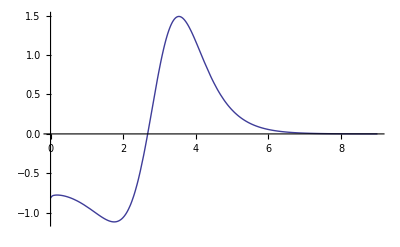

```mathematica
Plot[{tbppf[b]},{b,0,9}]
```

```mathematica
phi3 is eq 18 without constants
```

```mathematica
(Deriv wrt r )^2
```

```mathematica
Clear[R,aws];(Exp[(r-R)/aws]/aws)^2/(1+Exp[(r-R)/aws])^4/.r->Sqrt[b^2+z^2]
```

(ⅇ^((2 (-R+√(b^2+z^2)))/aws))/(aws^2 (1+ⅇ^((-R+√(b^2+z^2))/aws))^4)

```mathematica
Clear[R,aws];FullSimplify[ (ⅇ^((2 (-R+√(b^2+z^2)))/aws))/(aws^2 (1+ⅇ^((-R+√(b^2+z^2))/aws))^4)+5/3b D[(ⅇ^((2 (-R+√(b^2+z^2)))/aws))/(aws^2 (1+ⅇ^((-R+√(b^2+z^2))/aws))^4),b]+b^2/3 D[ (ⅇ^((2 (-R+√(b^2+z^2)))/aws))/(aws^2 (1+ⅇ^((-R+√(b^2+z^2))/aws))^4),{b,2}] ]
```

1/(96 aws^4 (b^2+z^2)^(3/2))Sech[(R-√(b^2+z^2))/(2 aws)]^6 (3 √(b^2+z^2) (-2 b^4+aws^2 (b^2+z^2))+√(b^2+z^2) (4 b^4+3 aws^2 (b^2+z^2)) Cosh[(R-√(b^2+z^2))/aws]+2 aws b^2 (5 b^2+6 z^2) Sinh[(R-√(b^2+z^2))/aws])

```mathematica
phi3b[b_,R_,aws_]:=NIntegrate[1/(96 aws^4 (b^2+z^2)^(3/2))Sech[(R-√(b^2+z^2))/(2 aws)]^6 (3 √(b^2+z^2) (-2 b^4+aws^2 (b^2+z^2))+√(b^2+z^2) (4 b^4+3 aws^2 (b^2+z^2)) Cosh[(R-√(b^2+z^2))/aws]+2 aws b^2 (5 b^2+6 z^2) Sinh[(R-√(b^2+z^2))/aws]),{z,-15,15}]
```

```mathematica
phi3b[1.1,R,aws]
```

0.972525

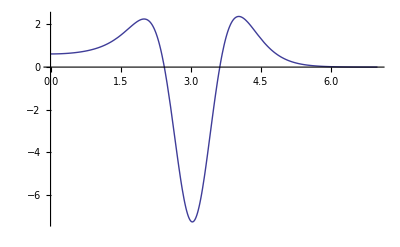

```mathematica
R=3;aws=0.54;Plot[phi3b[b,R,aws],{b,0,7},PlotRange->All]
```

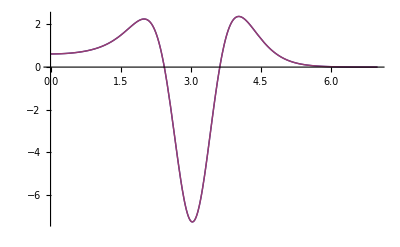

```mathematica
Plot[{phi3b[b,R,aws],phi3f[b]},{b,0,7},PlotRange->All]
```

```mathematica
phi3t=Table[{.05j,phi3b[.05j,R,aws]},{j,0,300}]
```

{{0.,0.617257},{0.05,0.617766},{0.1,0.619295},{0.15,0.621853},{0.2,0.625462},{0.25,0.630154},{0.3,0.635973},{0.35,0.642972},{0.4,0.651217},{0.45,0.660785},{0.5,0.671769},{0.55,0.684276},{0.6,0.69843},{0.65,0.714374},{0.7,0.732269},{0.75,0.752298},{0.8,0.774667},{0.85,0.799605},{0.9,0.827366},{0.95,0.858228},{1.,0.892492},{1.05,0.930479},{1.1,0.972525},{1.15,1.01898},{1.2,1.07017},{1.25,1.12643},{1.3,1.18804},{1.35,1.25522},{1.4,1.32806},{1.45,1.40653},{1.5,1.49039},{1.55,1.57909},{1.6,1.67178},{1.65,1.76711},{1.7,1.86322},{1.75,1.95758},{1.8,2.04691},{1.85,2.12704},{1.9,2.1929},{1.95,2.2384},{2.,2.25652},{2.05,2.23929},{2.1,2.17807},{2.15,2.06375},{2.2,1.88725},{2.25,1.63999},{2.3,1.31465},{2.35,0.905926},{2.4,0.411401},{2.45,-0.167618},{2.5,-0.825321},{2.55,-1.55083},{2.6,-2.32795},{2.65,-3.13523},{2.7,-3.94663},{2.75,-4.73256},{2.8,-5.46146},{2.85,-6.10168},{2.9,-6.62367},{2.95,-7.00209},{3.,-7.21784},{3.05,-7.2595},{3.1,-7.12436},{3.15,-6.8186},{3.2,-6.3568},{3.25,-5.76079},{3.3,-5.05793},{3.35,-4.27912},{3.4,-3.45656},{3.45,-2.62176},{3.5,-1.8037},{3.55,-1.02746},{3.6,-0.313237},{3.65,0.324035},{3.7,0.874772},{3.75,1.33437},{3.8,1.70262},{3.85,1.98293},{3.9,2.18147},{3.95,2.30636},{4.,2.36691},{4.05,2.37292},{4.1,2.33414},{4.15,2.25988},{4.2,2.15872},{4.25,2.03827},{4.3,1.90515},{4.35,1.76493},{4.4,1.62217},{4.45,1.48051},{4.5,1.34274},{4.55,1.21091},{4.6,1.08647},{4.65,0.970325},{4.7,0.862977},{4.75,0.764593},{4.8,0.675086},{4.85,0.594181},{4.9,0.521469},{4.95,0.456452},{5.,0.398579},{5.05,0.347277},{5.1,0.301966},{5.15,0.262078},{5.2,0.22707},{5.25,0.196428},{5.3,0.169675},{5.35,0.146368},{5.4,0.126107},{5.45,0.108526},{5.5,0.0932963},{5.55,0.0801251},{5.6,0.0687504},{5.65,0.0589403},{5.7,0.05049},{5.75,0.0432193},{5.8,0.0369701},{5.85,0.0316041},{5.9,0.0270007},{5.95,0.0230547},{6.,0.019675},{6.05,0.0167823},{6.1,0.0143082},{6.15,0.0121934},{6.2,0.0103869},{6.25,0.00884445},{6.3,0.00752825},{6.35,0.00640564},{6.4,0.00544859},{6.45,0.00463303},{6.5,0.00393833},{6.55,0.00334682},{6.6,0.00284335},{6.65,0.00241497},{6.7,0.0020506},{6.75,0.00174078},{6.8,0.00147741},{6.85,0.00125361},{6.9,0.00106347},{6.95,0.000901976},{7.,0.00076485},{7.05,0.000648441},{7.1,0.000549644},{7.15,0.000465812},{7.2,0.000394695},{7.25,0.000334376},{7.3,0.000283227},{7.35,0.000239862},{7.4,0.000203104},{7.45,0.000171951},{7.5,0.000145554},{7.55,0.000123191},{7.6,0.000104249},{7.65,0.000088206},{7.7,0.0000746215},{7.75,0.0000631205},{7.8,0.0000533848},{7.85,0.0000451448},{7.9,0.0000381716},{7.95,0.0000322714},{8.,0.0000272798},{8.05,0.0000230574},{8.1,0.0000194862},{8.15,0.0000164662},{8.2,0.0000139126},{8.25,0.0000117537},{8.3,9.92862×10^-6},{8.35,8.38603×10^-6},{8.4,7.08233×10^-6},{8.45,5.98066×10^-6},{8.5,5.04982×10^-6},{8.55,4.26342×10^-6},{8.6,3.59911×10^-6},{8.65,3.038×10^-6},{8.7,2.56411×10^-6},{8.75,2.16393×10^-6},{8.8,1.82602×10^-6},{8.85,1.54074×10^-6},{8.9,1.2999×10^-6},{8.95,1.0966×10^-6},{9.,9.25018×10^-7},{9.05,7.80209×10^-7},{9.1,6.5801×10^-7},{9.15,5.54902×10^-7},{9.2,4.67909×10^-7},{9.25,3.9452×10^-7},{9.3,3.32613×10^-7},{9.35,2.80397×10^-7},{9.4,2.36358×10^-7},{9.45,1.99219×10^-7},{9.5,1.67903×10^-7},{9.55,1.41498×10^-7},{9.6,1.19236×10^-7},{9.65,1.00468×10^-7},{9.7,8.46482×10^-8},{9.75,7.13137×10^-8},{9.8,6.00753×10^-8},{9.85,5.06041×10^-8},{9.9,4.26229×10^-8},{9.95,3.58979×10^-8},{10.,3.02317×10^-8},{10.05,2.54581×10^-8},{10.1,2.14367×10^-8},{10.15,1.80493×10^-8},{10.2,1.51961×10^-8},{10.25,1.2793×10^-8},{10.3,1.07692×10^-8},{10.35,9.06498×10^-9},{10.4,7.62993×10^-9},{10.45,6.42164×10^-9},{10.5,5.40434×10^-9},{10.55,4.5479×10^-9},{10.6,3.82694×10^-9},{10.65,3.22007×10^-9},{10.7,2.70926×10^-9},{10.75,2.27935×10^-9},{10.8,1.91753×10^-9},{10.85,1.61305×10^-9},{10.9,1.35684×10^-9},{10.95,1.14126×10^-9},{11.,9.59868×10^-10},{11.05,8.07262×10^-10},{11.1,6.78879×10^-10},{11.15,5.70881×10^-10},{11.2,4.80036×10^-10},{11.25,4.03625×10^-10},{11.3,3.39358×10^-10},{11.35,2.85308×10^-10},{11.4,2.39853×10^-10},{11.45,2.01629×10^-10},{11.5,1.69488×10^-10},{11.55,1.42463×10^-10},{11.6,1.1974×10^-10},{11.65,1.00637×10^-10},{11.7,8.45768×10^-11},{11.75,7.1076×10^-11},{11.8,5.97273×10^-11},{11.85,5.01881×10^-11},{11.9,4.21703×10^-11},{11.95,3.54317×10^-11},{12.,2.97684×10^-11},{12.05,2.50091×10^-11},{12.1,2.10097×10^-11},{12.15,1.7649×10^-11},{12.2,1.48252×10^-11},{12.25,1.24526×10^-11},{12.3,1.04593×10^-11},{12.35,8.78457×10^-12},{12.4,7.37769×10^-12},{12.45,6.19585×10^-12},{12.5,5.20309×10^-12},{12.55,4.36921×10^-12},{12.6,3.66881×10^-12},{12.65,3.08055×10^-12},{12.7,2.5865×10^-12},{12.75,2.17159×10^-12},{12.8,1.82316×10^-12},{12.85,1.53058×10^-12},{12.9,1.28489×10^-12},{12.95,1.07859×10^-12},{13.,9.05383×10^-13},{13.05,7.59957×10^-13},{13.1,6.37864×10^-13},{13.15,5.35365×10^-13},{13.2,4.49318×10^-13},{13.25,3.77086×10^-13},{13.3,3.16454×10^-13},{13.35,2.65561×10^-13},{13.4,2.22843×10^-13},{13.45,1.8699×10^-13},{13.5,1.569×10^-13},{13.55,1.31646×10^-13},{13.6,1.10453×10^-13},{13.65,9.26686×10^-14},{13.7,7.77446×10^-14},{13.75,6.52217×10^-14},{13.8,5.4714×10^-14},{13.85,4.58975×10^-14},{13.9,3.85003×10^-14},{13.95,3.22941×10^-14},{14.,2.70874×10^-14},{14.05,2.27194×10^-14},{14.1,1.9055×10^-14},{14.15,1.59812×10^-14},{14.2,1.34027×10^-14},{14.25,1.12399×10^-14},{14.3,9.42575×10^-15},{14.35,7.90416×10^-15},{14.4,6.62798×10^-15},{14.45,5.55767×10^-15},{14.5,4.66004×10^-15},{14.55,3.90726×10^-15},{14.6,3.27597×10^-15},{14.65,2.7466×10^-15},{14.7,2.30269×10^-15},{14.75,1.93047×10^-15},{14.8,1.61837×10^-15},{14.85,1.35668×10^-15},{14.9,1.13727×10^-15},{14.95,9.53315×10^-16},{15.,7.99091×10^-16}}

```mathematica
phi3f=Interpolation[phi3t]
```

InterpolatingFunction[{{0.,15.}},<>]

```mathematica
aws
```

aws

```mathematica
aws=.54
```

0.54

```mathematica
R
```

R

```mathematica
R=3
```

3

```mathematica
R
```

R

```mathematica
R=3;aws=0.54
```

0.54

```mathematica
FeikWS2[V,1,R,0]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3 + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1 + ⅇ^1.85185\ (-3 + √Plus[« 2 »])\ (1 - 3.7037\ b^2/√Power[« 2 »] + Power[« 2 »])/(1 + ⅇ^1.85185\ (-3 + √Plus[« 2 »]))^3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

4.1894+10.5113 ⅈ

```mathematica
Table[{FeikWS[V,k,R,0],FeikWS1[V,k,R,0],FeikWS2[V,k,R,0]},{k,1,3}]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3 + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{{3.22489+8.21064 ⅈ,1.61739+9.6372 ⅈ,4.1894+10.5113 ⅈ},{9.63498+12.5841 ⅈ,10.0328+13.877 ⅈ,10.4083+11.8393 ⅈ},{14.1432+12.2368 ⅈ,14.5428+12.7533 ⅈ,14.1389+11.4673 ⅈ}}

```mathematica
Table[{FeikWS[V,k,R,0],FeikWS1[V,k,R,0],FeikWS2[V,k,R,0]},{k,1,3}]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3 + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{{3.22489+8.21064 ⅈ,1.61739+9.6372 ⅈ,3.46512+10.6936 ⅈ},{9.63498+12.5841 ⅈ,10.0328+13.877 ⅈ,10.5282+12.7535 ⅈ},{14.1432+12.2368 ⅈ,14.5428+12.7533 ⅈ,14.4778+12.1085 ⅈ}}

```mathematica
SetDirectory["~/Documents/gb"]
```

/Users/miller/Documents/gb

```mathematica
xxx=Import[ "fort.76"]
```

{{138.49},{133.63},{119.988},{100.093},{77.3482},{55.1328},{36.0493},{21.5218},{11.7908},{6.20598},{3.64725},{2.91887},{3.02053},{3.27206},{3.31793},{3.059},{2.55753},{1.94739},{1.36606},{0.913091},{0.632702},{0.515375},{0.512334},{0.556878},{0.586762},{0.562397},{0.476846},{0.355579},{0.246499},{0.203274},{0.266861},{0.450658},{0.733705},{1.06409},{1.37171},{1.58683},{1.65907},{295.039},{263.894},{188.21},{105.878},{46.0833},{15.3768},{4.64407},{2.42931},{2.04013},{1.47441},{0.808544},{0.358925},{0.164895},{0.109174},{0.0890516},{0.0660594},{0.0409911},{0.0221239},{0.0119422},{0.00783348},{0.00627613},{0.00515824},{0.00388326},{0.0026069},{0.00159142},{0.000944679},{0.000620462},{0.000499765},{0.000458762},{0.000408684},{0.000316167},{0.000203239},{0.000121836},{0.000111741},{0.000167676},{0.000240002},{0.000270064},{373.853},{295.339},{143.373},{40.2793},{6.02962},{1.3945},{1.0823},{0.460676},{0.108563},{0.0416857},{0.0300486},{0.0139056},{0.00423362},{0.00180802},{0.00127456},{0.000688384},{0.000257885},{0.000101751},{0.000066382},{0.0000445495},{0.0000220433},{8.49304×10^-6},{3.71606×10^-6},{2.43528×10^-6},{1.66408×10^-6},{8.86016×10^-7},{3.31415×10^-7},{9.01002×10^-8},{3.79496×10^-8},{3.65724×10^-8},{3.00421×10^-8},{1.64813×10^-8},{4.84923×10^-9},{1.94127×10^-10},{2.90153×10^-9},{8.81338×10^-9},{1.15769×10^-8}}

```mathematica
xxx[[2]]
```

{133.63}

```mathematica
sig1=Table[{5j,xxx[[j+1]]},{j,0,36}]
```

{{0,{138.49}},{5,{133.63}},{10,{119.988}},{15,{100.093}},{20,{77.3482}},{25,{55.1328}},{30,{36.0493}},{35,{21.5218}},{40,{11.7908}},{45,{6.20598}},{50,{3.64725}},{55,{2.91887}},{60,{3.02053}},{65,{3.27206}},{70,{3.31793}},{75,{3.059}},{80,{2.55753}},{85,{1.94739}},{90,{1.36606}},{95,{0.913091}},{100,{0.632702}},{105,{0.515375}},{110,{0.512334}},{115,{0.556878}},{120,{0.586762}},{125,{0.562397}},{130,{0.476846}},{135,{0.355579}},{140,{0.246499}},{145,{0.203274}},{150,{0.266861}},{155,{0.450658}},{160,{0.733705}},{165,{1.06409}},{170,{1.37171}},{175,{1.58683}},{180,{1.65907}}}

```mathematica
sig1f=Interpolation[sig1]
```

InterpolatingFunction[{{0.,180.}},<>]

```mathematica
sig1f[9]
```

{123.297}

```mathematica
sig2=Table[{5j,xxx[[j+38]]},{j,0,36}]
```

{{0,{295.039}},{5,{263.894}},{10,{188.21}},{15,{105.878}},{20,{46.0833}},{25,{15.3768}},{30,{4.64407}},{35,{2.42931}},{40,{2.04013}},{45,{1.47441}},{50,{0.808544}},{55,{0.358925}},{60,{0.164895}},{65,{0.109174}},{70,{0.0890516}},{75,{0.0660594}},{80,{0.0409911}},{85,{0.0221239}},{90,{0.0119422}},{95,{0.00783348}},{100,{0.00627613}},{105,{0.00515824}},{110,{0.00388326}},{115,{0.0026069}},{120,{0.00159142}},{125,{0.000944679}},{130,{0.000620462}},{135,{0.000499765}},{140,{0.000458762}},{145,{0.000408684}},{150,{0.000316167}},{155,{0.000203239}},{160,{0.000121836}},{165,{0.000111741}},{170,{0.000167676}},{175,{0.000240002}},{180,{0.000270064}}}

```mathematica
sig2f=Interpolation[sig2]
```

InterpolatingFunction[{{0.,180.}},<>]

```mathematica
sig3=Table[{5j,xxx[[j+75]]},{j,0,36}]
```

{{0,{373.853}},{5,{295.339}},{10,{143.373}},{15,{40.2793}},{20,{6.02962}},{25,{1.3945}},{30,{1.0823}},{35,{0.460676}},{40,{0.108563}},{45,{0.0416857}},{50,{0.0300486}},{55,{0.0139056}},{60,{0.00423362}},{65,{0.00180802}},{70,{0.00127456}},{75,{0.000688384}},{80,{0.000257885}},{85,{0.000101751}},{90,{0.000066382}},{95,{0.0000445495}},{100,{0.0000220433}},{105,{8.49304×10^-6}},{110,{3.71606×10^-6}},{115,{2.43528×10^-6}},{120,{1.66408×10^-6}},{125,{8.86016×10^-7}},{130,{3.31415×10^-7}},{135,{9.01002×10^-8}},{140,{3.79496×10^-8}},{145,{3.65724×10^-8}},{150,{3.00421×10^-8}},{155,{1.64813×10^-8}},{160,{4.84923×10^-9}},{165,{1.94127×10^-10}},{170,{2.90153×10^-9}},{175,{8.81338×10^-9}},{180,{1.15769×10^-8}}}

```mathematica
sig3f=Interpolation[sig3]
```

InterpolatingFunction[{{0.,180.}},<>]

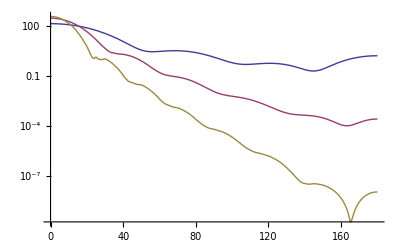

```mathematica
LogPlot[{sig1f[th],sig2f[th],sig3f[th]},{th,0,180}]
```

```mathematica
eik1=Table[{5 j,Abs[FeikWS[V,1,R,5 j Pi/180.]]^2},{j,0,36}]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3. + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{{0,77.8145},{5,75.1652},{10,67.7341},{15,56.9131},{20,44.558},{25,32.4905},{30,22.0902},{35,14.0933},{40,8.60979},{45,5.29653},{50,3.58484},{55,2.88107},{60,2.69497},{65,2.69096},{70,2.68203},{75,2.59347},{80,2.41948},{85,2.18657},{90,1.92896},{95,1.67551},{100,1.44515},{105,1.2471},{110,1.08335},{115,0.951461},{120,0.846852},{125,0.764427},{130,0.699464},{135,0.648019},{140,0.607018},{145,0.574175},{150,0.547852},{155,0.526903},{160,0.510546},{165,0.498253},{170,0.489682},{175,0.484616},{180,0.48294}}

```mathematica
eik1f=Interpolation[eik1]
```

```mathematica
eik11=Table[{5 j,Abs[FeikWS1[V,1,R,5 j Pi/180.]]^2},{j,0,36}]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3. + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1 + ⅇ^1.85185\ (-3. + √Plus[« 2 »])\ (1 - 3.7037\ b^2/√Power[« 2 »] + Power[« 2 »])/(1 + ⅇ^1.85185\ (-3. + √Plus[« 2 »]))^3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{{0,95.4916},{5,92.2997},{10,83.3414},{15,70.2796},{20,55.3313},{25,40.6714},{30,27.9463},{35,18.0332},{40,11.0649},{45,6.6403},{50,4.09939},{55,2.7633},{60,2.08345},{65,1.69602},{70,1.40711},{75,1.14374},{80,0.89979},{85,0.693667},{90,0.542989},{95,0.454218},{100,0.422058},{105,0.433466},{110,0.472584},{115,0.524609},{120,0.578},{125,0.62518},{130,0.662222},{135,0.688032},{140,0.703411},{145,0.710211},{150,0.710704},{155,0.707151},{160,0.701563},{165,0.695584},{170,0.69046},{175,0.687052},{180,0.685861}}

```mathematica
eik11f=Interpolation[eik11]
```

InterpolatingFunction[{{0.,180.}},<>]

```mathematica
eik112=Table[{5 j,Abs[FeikWS2[V,1,R,5 j Pi/180.]]^2},{j,0,36}]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3 + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1 + ⅇ^1.85185\ (-3 + √Plus[« 2 »])\ (1 - 3.7037\ b^2/√Power[« 2 »] + Power[« 2 »])/(1 + ⅇ^1.85185\ (-3 + √Plus[« 2 »]))^3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{{0,128.038},{5,123.565},{10,111.006},{15,92.6823},{20,71.7099},{25,51.1744},{30,33.4487},{35,19.8359},{40,10.5756},{45,5.11428},{50,2.48268},{55,1.64086},{60,1.70953},{65,2.07227},{70,2.37642},{75,2.47657},{80,2.36038},{85,2.0824},{90,1.71702},{95,1.33135},{100,0.973773},{105,0.672304},{110,0.438026},{115,0.270129},{120,0.160752},{125,0.0987955},{130,0.0725434},{135,0.0712248},{140,0.0857834},{145,0.109102},{150,0.135905},{155,0.162482},{160,0.18637},{165,0.206018},{170,0.220516},{175,0.22937},{180,0.232344}}

```mathematica
eik12f=Interpolation[eik112]
```

InterpolatingFunction[{{0.,180.}},<>]

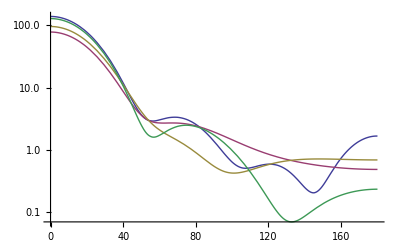

```mathematica
LogPlot[{sig1f[th],eik1f[th],eik11f[th],eik12f[th]},{th,0,180},PlotRange->All]
```

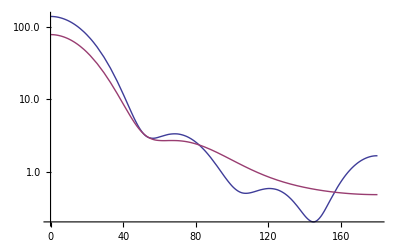

```mathematica
LogPlot[{sig1f[th],eik1f[th],eik11f[th],eik12f[th]},{th,0,180},PlotRange->All]
```

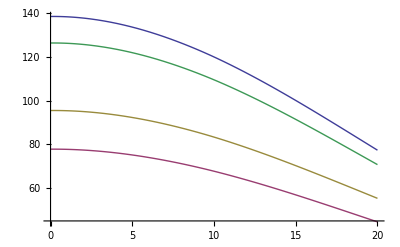

```mathematica
Plot[{sig1f[th],eik1f[th],eik11f[th],eik12f[th]},{th,0,20},PlotRange->All]
```

```mathematica
eik2=Table[{5 j,Abs[FeikWS[V,2,R,5 j Pi/180.]]^2},{j,0,36}]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3. + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{{0,251.192},{5,225.561},{10,163.141},{15,94.7649},{20,44.1986},{25,17.0379},{30,6.36467},{35,3.24731},{40,2.27455},{45,1.5768},{50,0.947942},{55,0.505763},{60,0.264224},{65,0.152662},{70,0.100683},{75,0.0700646},{80,0.0476932},{85,0.0310413},{90,0.0196277},{95,0.0124853},{100,0.00827408},{105,0.00580834},{110,0.00428852},{115,0.00326826},{120,0.00252973},{125,0.00197321},{130,0.00154989},{135,0.00123008},{140,0.000991259},{145,0.000814883},{150,0.000685829},{155,0.000592275},{160,0.000525389},{165,0.000478845},{170,0.00044831},{175,0.000431011},{180,0.000425409}}

```mathematica
eik2f=Interpolation[eik2]
```

```mathematica
eik21=Table[{5 j,Abs[FeikWS1[V,2,R,5 j Pi/180.]]^2},{j,0,36}]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3. + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1 + ⅇ^1.85185\ (-3. + √Plus[« 2 »])\ (1 - 3.7037\ b^2/√Power[« 2 »] + Power[« 2 »])/(1 + ⅇ^1.85185\ (-3. + √Plus[« 2 »]))^3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{{0,293.229},{5,262.662},{10,188.223},{15,106.828},{20,47.1341},{25,15.9455},{30,4.71483},{35,2.30389},{40,1.97682},{45,1.54029},{50,0.940713},{55,0.480324},{60,0.244116},{65,0.154793},{70,0.12076},{75,0.0957426},{80,0.070195},{85,0.0477625},{90,0.0316551},{95,0.0217224},{100,0.0160269},{105,0.0126165},{110,0.0102522},{115,0.00836894},{120,0.00678913},{125,0.00548236},{130,0.00444089},{135,0.00364071},{140,0.00304254},{145,0.00260282},{150,0.00228231},{155,0.00204985},{160,0.00188275},{165,0.00176541},{170,0.00168764},{175,0.00164319},{180,0.00162873}}

```mathematica
eik21f=Interpolation[eik21]
```

InterpolatingFunction[{{0.,180.}},<>]

```mathematica
eik22=Table[{5 j,Abs[FeikWS2[V,2,R,5 j Pi/180.]]^2},{j,0,36}]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3 + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1 + ⅇ^1.85185\ (-3 + √Plus[« 2 »])\ (1 - 3.7037\ b^2/√Power[« 2 »] + Power[« 2 »])/(1 + ⅇ^1.85185\ (-3 + √Plus[« 2 »]))^3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{{0,256.933},{5,225.12},{10,151.801},{15,80.8548},{20,38.6178},{25,21.5884},{30,14.2141},{35,7.77887},{40,2.68575},{45,1.00525},{50,1.90226},{55,2.91845},{60,2.69556},{65,1.62263},{70,0.700233},{75,0.435542},{80,0.658758},{85,0.944324},{90,1.01515},{95,0.851018},{100,0.581003},{105,0.340941},{110,0.199142},{115,0.155274},{120,0.17319},{125,0.212822},{130,0.246894},{135,0.263708},{140,0.262784},{145,0.249094},{150,0.228782},{155,0.206938},{160,0.186941},{165,0.170643},{170,0.158844},{175,0.151768},{180,0.149417}}

```mathematica
eik22f=Interpolation[eik22]
```

InterpolatingFunction[{{0.,180.}},<>]

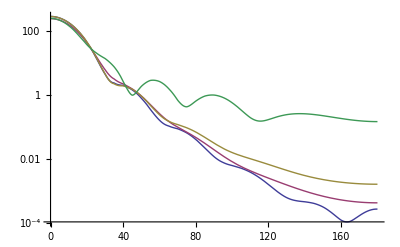

```mathematica
LogPlot[{sig2f[th],eik2f[th],eik21f[th],eik22f[th]},{th,0,180},PlotRange->All]
```

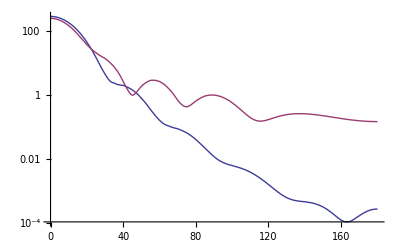

```mathematica
LogPlot[{sig2f[th],eik22f[th]},{th,0,180},PlotRange->All]
```

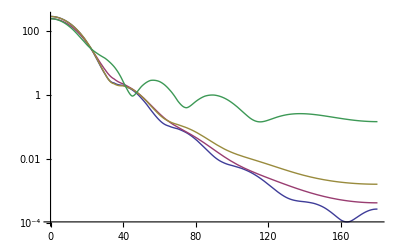

```mathematica
LogPlot[{sig2f[th],eik2f[th],eik21f[th],eik22f[th]},{th,0,180},PlotRange->All]
```

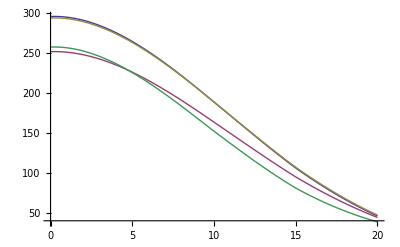

```mathematica
Plot[{sig2f[th],eik2f[th],eik21f[th],eik22f[th]},{th,0,20},PlotRange->All]
```

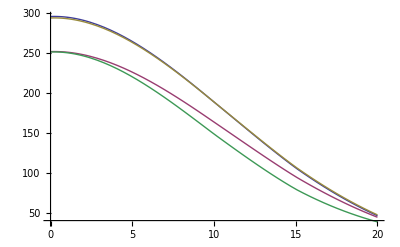

```mathematica
Plot[{sig2f[th],eik2f[th],eik21f[th],eik22f[th]},{th,0,20},PlotRange->All]
```

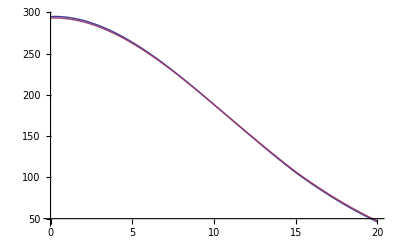

```mathematica
Plot[{sig2f[th],eik21f[th]},{th,0,20},PlotRange->All]
```

```mathematica
Plot[{sig1f[th],Abs[FeikWS[V,1,R,aws,th]]^2},{th,0,180}]
```

```mathematica
eik3=Table[{5 j,Abs[FeikWS[V,3,R,5 j Pi/180.]]^2},{j,0,36}]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3. + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{{0,349.768},{5,277.776},{10,137.768},{15,41.1815},{20,7.33388},{25,1.67085},{30,1.03981},{35,0.478005},{40,0.141437},{45,0.047416},{50,0.0261361},{55,0.0132275},{60,0.00515564},{65,0.00199315},{70,0.00101812},{75,0.000574928},{80,0.000288599},{85,0.000131076},{90,0.0000627925},{95,0.0000352951},{100,0.0000216622},{105,0.0000130888},{110,7.59938×10^-6},{115,4.39071×10^-6},{120,2.66059×10^-6},{125,1.74373×10^-6},{130,1.22719×10^-6},{135,9.03796×10^-7},{140,6.82693×10^-7},{145,5.25059×10^-7},{150,4.11897×10^-7},{155,3.31478×10^-7},{160,2.7538×10^-7},{165,2.37385×10^-7},{170,2.13083×10^-7},{175,1.9958×10^-7},{180,1.95252×10^-7}}

```mathematica
eik3f=Interpolation[eik3]
```

InterpolatingFunction[{{0.,180.}},<>]

```mathematica
eik31=Table[{5 j,Abs[FeikWS1[V,3,R,5 j Pi/180.]]^2},{j,0,36}]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3. + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1 + ⅇ^1.85185\ (-3. + √Plus[« 2 »])\ (1 - 3.7037\ b^2/√Power[« 2 »] + Power[« 2 »])/(1 + ⅇ^1.85185\ (-3. + √Plus[« 2 »]))^3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{{0,374.138},{5,295.911},{10,144.219},{15,40.8059},{20,6.13047},{25,1.38653},{30,1.11834},{35,0.504547},{40,0.127554},{45,0.0473379},{50,0.0349572},{55,0.0185396},{60,0.00674401},{65,0.00277696},{70,0.00183645},{75,0.00118749},{80,0.000606985},{85,0.000279397},{90,0.000152078},{95,0.000103079},{100,0.0000710964},{105,0.0000449859},{110,0.0000267296},{115,0.0000161405},{120,0.000010636},{125,7.71019×10^-6},{130,5.90003×10^-6},{135,4.58958×10^-6},{140,3.57933×10^-6},{145,2.8071×10^-6},{150,2.23551×10^-6},{155,1.82612×10^-6},{160,1.54141×10^-6},{165,1.34989×10^-6},{170,1.22818×10^-6},{175,1.16087×10^-6},{180,1.13936×10^-6}}

```mathematica
eik31f=Interpolation[eik31]
```

InterpolatingFunction[{{0.,180.}},<>]

```mathematica
eik32=Table[{5 j,Abs[FeikWS2[V,3,R,5 j Pi/180.]]^2},{j,0,36}]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3 + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1 + ⅇ^1.85185\ (-3 + √Plus[« 2 »])\ (1 - 3.7037\ b^2/√Power[« 2 »] + Power[« 2 »])/(1 + ⅇ^1.85185\ (-3 + √Plus[« 2 »]))^3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{{0,304.017},{5,224.721},{10,99.0127},{15,45.4126},{20,26.0968},{25,5.42027},{30,1.1644},{35,7.35359},{40,5.81452},{45,0.929454},{50,0.851985},{55,2.3892},{60,1.72607},{65,0.369845},{70,0.138173},{75,0.497875},{80,0.520089},{85,0.228579},{90,0.0304845},{95,0.0394154},{100,0.111757},{105,0.126924},{110,0.0832098},{115,0.0316633},{120,0.00548268},{125,0.00535967},{130,0.0168858},{135,0.0274635},{140,0.0319333},{145,0.0307129},{150,0.0263088},{155,0.021055},{160,0.0163539},{165,0.0127677},{170,0.0103628},{175,0.00901147},{180,0.00857883}}

```mathematica
eik32f=Interpolation[eik31]
```

InterpolatingFunction[{{0.,180.}},<>]

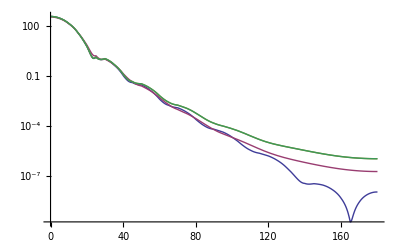

```mathematica
LogPlot[{sig3f[th],eik3f[th],eik31f[th],eik32f[th]},{th,0,180},PlotRange->All]
```

```mathematica
LogPlot[{sig3f[th],eik3f[th],eik31f[th],eik32f[th]},{th,0,180},PlotRange->All]
```

-Graphics-

```mathematica
LogPlot[{sig3f[th],eik3f[th],eik31f[th],eik32f[th]},{th,0,180},PlotRange->All]
```

-Graphics-

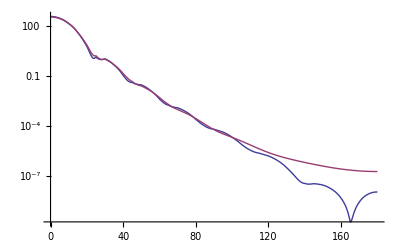

```mathematica
LogPlot[{sig3f[th],eik3f[th]},{th,0,180},PlotRange->All]
```

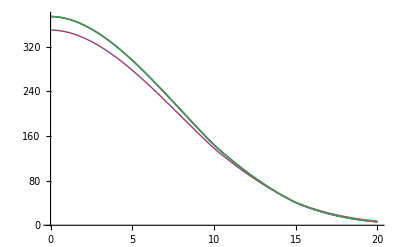

```mathematica
Plot[{sig3f[th],eik3f[th],eik31f[th],eik32f[th]},{th,0,20},PlotRange->All]
```

```mathematica
Plot[{sig3f[th],eik3f[th],eik31f[th],eik32f[th]},{th,0,20},PlotRange->All]
```

-Graphics-

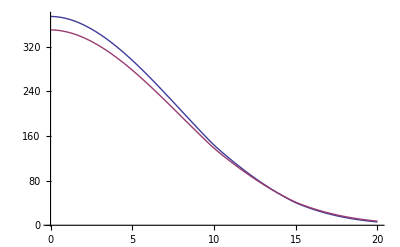

```mathematica
Plot[{sig3f[th],eik3f[th]},{th,0,20},PlotRange->All]
```

```mathematica
Abs[FeikWS[V,1,R,0]]^2
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3. + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

77.8145

```mathematica
aws=0.54
```

0.54

```mathematica
BesselJ[0,0]
```

1

```mathematica
FeikBorn[V_,k_,R_,theta_]:=1/I NIntegrate[ b BesselJ[0,2k Sin[theta/2]b](-I V/k Sqrt[R^2-b^2]),{b,0,R}]
```

```mathematica
Sigma[V_,k_,R_,th_,lmax_]:=Abs[f[V,k,R,Pi/180 th,lmax]]^2
```

```mathematica
Sigma[3, 180,13]
Table[{Sigma[V,k,R,0,15],SigmaEik[V,k,R,0]},{k,1,6}]
```

```mathematica
Table[{Sigma[V,k,R,0,35],SigmaEik[V,k,R,0]},{k,3,7}]
```

{{210.688,187.195},{233.996,219.284},{248.295,238.323},{257.863,250.692},{264.68,259.29}}

```mathematica
Table[{Sigma[V,k,R,0,15],SigmaEik[V,k,R,0]},{k,1,6}]
```

{{57.6129,20.2126},{109.22,83.9367},{131.958,117.675},{144.024,135.176},{151.115,145.462},{146.821,152.12}}

```mathematica
Table[{Sigma[V,k,R,0,35],SigmaEik[V,k,R,0]},{k,1,8}]
```

{{57.6129,20.2126},{109.22,83.9367},{131.958,117.675},{144.026,135.176},{151.441,145.462},{156.412,152.12},{159.962,156.741},{162.624,160.119}}

```mathematica
Table[{Sigma[V,k,R,0,35],SigmaEik[V,k,R,0]},{k,1,8}]
```

{{57.6129,20.2126},{109.22,83.9367},{131.958,117.675},{144.026,135.176},{151.441,145.462},{156.412,152.12},{159.962,156.741},{162.624,160.119}}

```mathematica
Table[SigmaEikWS[V,k,R,0],{k,3,7}]
```

```mathematica
Abs[1+2.I]^2
```

5.

```mathematica
Abs[f[V,1,R,0,15]]^2
```

57.6129

```mathematica
Sigma[V,1,R,0,15]
```

57.6129

```mathematica
Sigma[V,1,R,0,15]
```

57.6129

```mathematica
Sigma[3, 180,15]
```

0.00268199

```mathematica
SigmaEik[V_,k_,R_,th_]:=Abs[Feik[V,k,R,Pi/180 th]]^2
```

```mathematica
SigmaEikWS[V_,k_,R_,th_]:=Abs[FeikWS[V,k,R,Pi/180 th]]^2
```

```mathematica
k
```

3

```mathematica
V
```

-1.9-0.38 ⅈ

```mathematica
R
```

3

```mathematica
Table[SigmaEikWS[V,k,R,5 th],{th,0,36}]
```

NIntegrate::inumr: The integrand 1/1 + ⅇ^1.85185\ (-3 + √Power[« 2 »] + Power[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{681.437,525.163,238.948,67.016,20.0479,12.1633,6.74627,2.80875,1.2279,0.65983,0.3436,0.161,0.077401,0.0412558,0.0225111,0.0118345,0.00618811,0.0033991,0.00196956,0.00116428,0.000689176,0.00041245,0.000254645,0.000164022,0.000109937,0.0000760354,0.0000539534,0.0000392495,0.0000293466,0.0000226267,0.0000180358,0.0000148835,0.0000127215,0.0000112624,0.0000103255,9.80175×10^-6,9.63325×10^-6}

```mathematica
SigmaEik[3,180]
```

0.00782187

```mathematica
Abs[Feik[V,1,R,180]]^2
```

0.713761

```mathematica
Abs[Feik[V,1,R,90]]^2
```

0.656599

```mathematica
SigmaEik[V,3,R,0]
```

117.675

```mathematica
SigmaEik[V,3,R,0]
```

117.675

```mathematica
SigmaEik[V,1,R,10]
```

19.0526

```mathematica
R=3
```

3

```mathematica
Grid[Table[{f[V,k,R,0,35]},{k,3,7}]]
```

9.60054+10.8866 ⅈ
11.7006+9.8535 ⅈ
12.9531+8.97284 ⅈ
13.7642+8.27103 ⅈ
14.3246+7.71277 ⅈ

```mathematica
Grid[Table[{Feik[V,k,R,0]},{k,3,7}]]
```

8.92585+10.3694 ⅈ
11.2791+9.59508 ⅈ
12.6703+8.8197 ⅈ
13.5627+8.16973 ⅈ
14.1743+7.64072 ⅈ

```mathematica
xx=Table[{Feik[V,k,R,0]},{k,3,7}]
```

{{7.48346+7.85323 ⅈ},{9.14852+7.17499 ⅈ},{10.1185+6.56339 ⅈ},{10.7369+6.06942 ⅈ},{11.1596+5.67492 ⅈ}}

```mathematica
xx=Table[{th 5,Abs[Feik[V,1,R,th]]^2},{th,0,36}]
```

{{0,20.2126},{5,2.33976},{10,0.636871},{15,0.627209},{20,0.720223},{25,0.434733},{30,17.2887},{35,7.11601},{40,0.387215},{45,0.665122},{50,0.692592},{55,0.246941},{60,10.6695},{65,13.9633},{70,0.214821},{75,0.712901},{80,0.643615},{85,0.521097},{90,4.50238},{95,19.3447},{100,1.02239},{105,0.701076},{110,0.621937},{115,0.696086},{120,1.13784},{125,19.5339},{130,4.2021},{135,0.537202},{140,0.641178},{145,0.714876},{150,0.223093},{155,14.3892},{160,10.2314},{165,0.260063},{170,0.689425},{175,0.668305},{180,0.368722}}

```mathematica
xx=Table[{th 5,SigmaEik[V,1,R,th]},{th,0,36}]
```

{{0,20.2126},{5,20.2007},{10,20.165},{15,20.1056},{20,20.0227},{25,19.9167},{30,19.7877},{35,19.6363},{40,19.463},{45,19.2682},{50,19.0526},{55,18.8168},{60,18.5617},{65,18.288},{70,17.9965},{75,17.6881},{80,17.3639},{85,17.0246},{90,16.6714},{95,16.3053},{100,15.9273},{105,15.5386},{110,15.1401},{115,14.7331},{120,14.3186},{125,13.8977},{130,13.4716},{135,13.0414},{140,12.608},{145,12.1727},{150,11.7364},{155,11.3002},{160,10.865},{165,10.4319},{170,10.0017},{175,9.57536},{180,9.15374}}

```mathematica
xx=Table[{th 5,SigmaEik[V,1,R,th]},{th,0,36}]
```

{{0,20.2126},{5,20.2007},{10,20.165},{15,20.1056},{20,20.0227},{25,19.9167},{30,19.7877},{35,19.6363},{40,19.463},{45,19.2682},{50,19.0526},{55,18.8168},{60,18.5617},{65,18.288},{70,17.9965},{75,17.6881},{80,17.3639},{85,17.0246},{90,16.6714},{95,16.3053},{100,15.9273},{105,15.5386},{110,15.1401},{115,14.7331},{120,14.3186},{125,13.8977},{130,13.4716},{135,13.0414},{140,12.608},{145,12.1727},{150,11.7364},{155,11.3002},{160,10.865},{165,10.4319},{170,10.0017},{175,9.57536},{180,9.15374}}

```mathematica
Eik1=Interpolation[xx]
```

InterpolatingFunction[{{0.,180.}},<>]

```mathematica
Eik1[7.]
```

20.1892

```mathematica
R
```

3

```mathematica
Table[{Sigma[V,k,R,0,35],SigmaEik[V,k,R,0]},{k,1,7}]
```

{{85.8279,25.5718},{168.657,126.999},{210.688,187.195},{233.996,219.284},{248.295,238.323},{257.863,250.692},{264.68,259.29}}

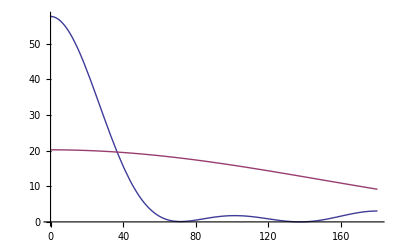

```mathematica
Plot[{Sigma[V,1,R,th,15],Eik1[th]},{th,0,180}]
```

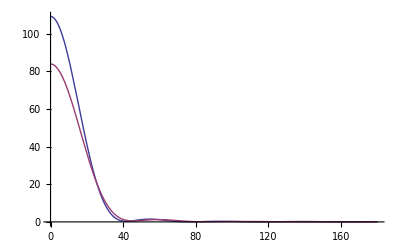

```mathematica
Plot[{Sigma[V,2,R,th,17],SigmaEik[V,2,R,th]},{th,0,180},PlotRange->All]
```

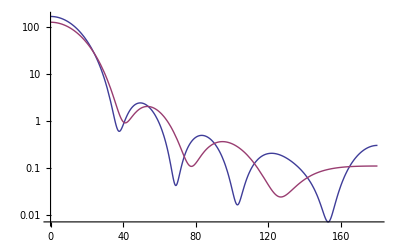

```mathematica
LogPlot[{Sigma[V,2,R,th,17],SigmaEik[V,2,R,th]},{th,0,180},PlotRange->All]
```

NIntegrate::inumr: The integrand b\ (-1 + ⅇ^(-0.19 + 0.95\ ⅈ)\ √7.56928  - Power[« 2 »])\ BesselJ[0, 4\ b\ Sin[π\ th/360]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 2.75123}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

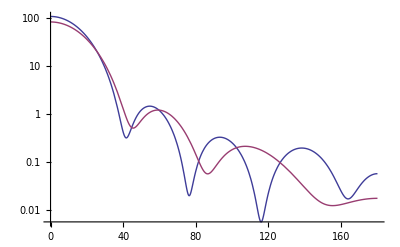

```mathematica
LogPlot[{Sigma[V,2,R,th,17],SigmaEik[V,2,R,th]},{th,0,180},PlotRange->All]
```

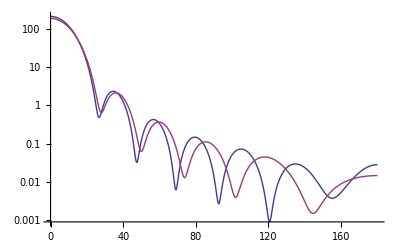

```mathematica
LogPlot[{Sigma[V,3,R,th,19],SigmaEik[V,3,R,th]},{th,0.0001,180},PlotRange->All]
```

NIntegrate::inumr: The integrand b\ (-1 + ⅇ^(-0.126667 + 0.633333\ ⅈ)\ √7.56928  - Power[« 2 »])\ BesselJ[0, 6\ b\ Sin[π\ th/360]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 2.75123}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

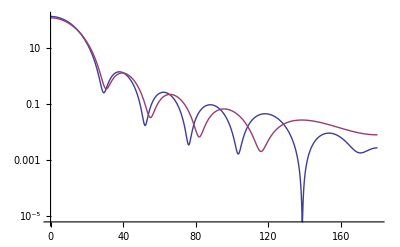

```mathematica
LogPlot[{Sigma[V,3,R,th,19],SigmaEik[V,3,R,th]},{th,0.0001,180},PlotRange->All]
```

```mathematica
P1=Plot[{Sigma[V,1,R,th, 15],SigmaEik[V,1,R,th],PlotRange->All},{th,0,180}]
```

-Graphics-

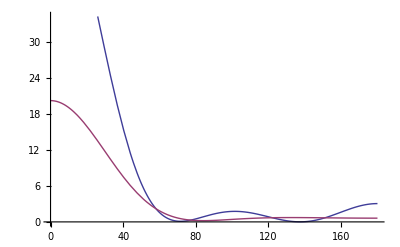

```mathematica
P1=Plot[{Sigma[V,1,R,th, 15],SigmaEik[V,1,R,th],PlotRange->All},{th,0,180}]
```

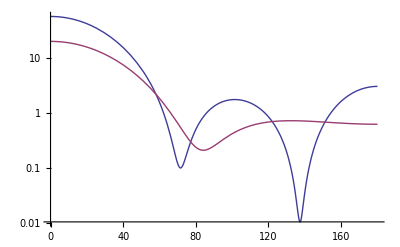

```mathematica
P1=LogPlot[{Sigma[1,th, 15],SigmaEik[1,th],PlotRange->All},{th,0,180}]
```

```mathematica
Sigma[2,0,15]
```

109.22

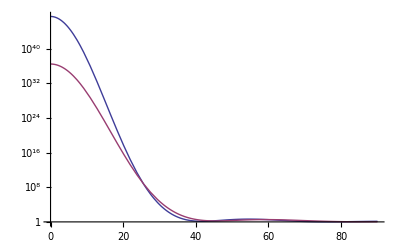

```mathematica
P2=LogPlot[{Sigma[2,th, 15],SigmaEik[2,th],PlotRange->All},{th,0,90}]
```

```mathematica
P2=LogPlot[{Sigma[2,th, 15],SigmaEik[2,th],PlotRange->All},{th,0,90}]
```

-Graphics-

```mathematica
P2=LogPlot[{Sigma[2,th, 15],SigmaEik[2,th],PlotRange->All},{th,0,90}]
```

-Graphics-

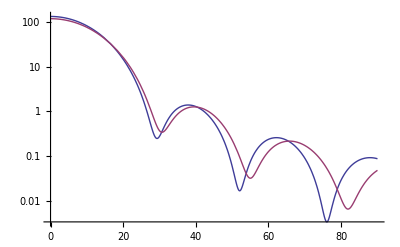

```mathematica
P3=LogPlot[{Sigma[3,th, 15],SigmaEik[3,th],PlotRange->All},{th,0,90}]
```

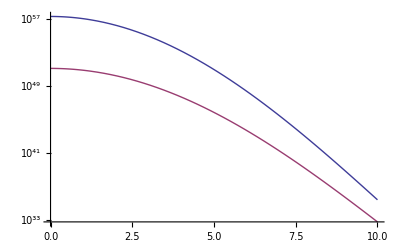

```mathematica
P3=LogPlot[{Sigma[3,th, 15],SigmaEik[3,th],PlotRange->All},{th,0,10}]
```

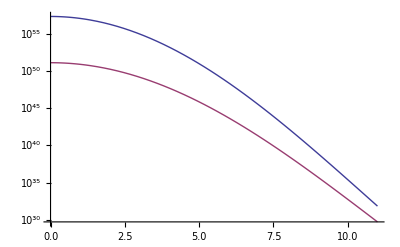

```mathematica
P33=LogPlot[{Sigma[3,th, 15],SigmaEik[3,th],PlotRange->All},{th,0,11}]
```

```mathematica
(*Feik[V_,k_,R_,theta_]:=k/I NIntegrate[ b BesselJ[0,2k Sin[theta/2]b](Exp[-I V/k Sqrt[R^2-b^2]]-1),{b,0,R}]
```

```mathematica
Clear[R,V,k];k/I Integrate[ b (Exp[-I V/k Sqrt[R^2-b^2]]-1),{b,0,R}]
```

-ⅈ k (-R^2/2+(k (-k+ⅇ^(-(ⅈ √(R^2) V)/k) (k+ⅈ √(R^2) V)))/V^2)

```mathematica
Clear[R,V,k]
```

```mathematica
ComplexExpand[- ⅈ k (-R^2/2+(k (-k+ⅇ^(-(ⅈ √(R^2) V)/k) (k+ⅈ √(R^2) V)))/V^2)4 Pi/k ]/.√(R^2)->R
```

(4 k π R Cos[(R V)/k])/V-(4 k^2 π Sin[(R V)/k])/V^2+ⅈ (2 π R^2+(4 k^2 π)/V^2-(4 k^2 π Cos[(R V)/k])/V^2-(4 k π R Sin[(R V)/k])/V)

```mathematica
FeikAnal[k_]:=(4 k π R Cos[(R V)/k])/V-(4 k^2 π Sin[(R V)/k])/V^2+ⅈ (2 π R^2+(4 k^2 π)/V^2-(4 k^2 π Cos[(R V)/k])/V^2-(4 k π R Sin[(R V)/k])/V)
```

```mathematica
FeikAnal[2]
```

27.3102+50.6738 ⅈ

```mathematica
k=2;theta=0
```

0

```mathematica
Feik[V,2,R,0]
```

4.34656+8.06499 ⅈ

```mathematica
k/I NIntegrate[ b BesselJ[0,2k Sin[theta/2]b](Exp[-I V/k Sqrt[R^2-b^2]]-1),{b,0,R}]
```

4.34656+8.06499 ⅈ

```mathematica
Feik[V,k,R,0]
```

4.34656+8.06499 ⅈ

```mathematica
Abs[Feik[V,k,R,0]]^2
```

83.9367

```mathematica
f[V,k,R,0,15]
```

5.2332+9.04617 ⅈ

```mathematica
Table[{ Abs[f[V,k,R,th Pi/10,15]]^2,Abs[Feik[V,k,R,th]]^2},{th,0,10}]
```

{{109.22,83.9367},{50.1398,1.20309},{1.84971,0.188388},{1.47168,0.0167226},{0.109246,0.0691137},{0.311498,0.448138},{0.0811182,48.9567},{0.0928497,0.990971},{0.173217,0.167542},{0.0189232,0.0125008},{0.0577994,0.0162864}}

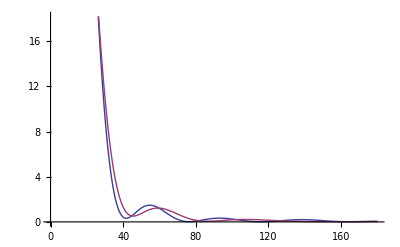

```mathematica
Plot[{ Abs[f[V,k,R,th Pi/180,15]]^2,Abs[Feik[V,k,R,th Pi/180]]^2},{th,0,180}]
```

```mathematica
LogPlot[{ Abs[f[V,k,R,th Pi/180,15]]^2,Abs[Feik[V,k,R,th Pi/180]]^2},{th,0,180}]
```

-Graphics-

```mathematica
k=1;LogPlot[{ Abs[f[V,k,R,th Pi/180,15]]^2,Abs[Feik[V,k,R,th Pi/180]]^2},{th,0,180}]
```

-Graphics-

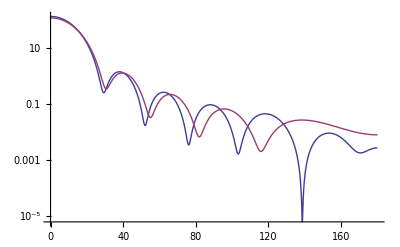

```mathematica
k=3;LogPlot[{ Abs[f[V,k,R,th Pi/180,15]]^2,Abs[Feik[V,k,R,th Pi/180]]^2},{th,0,180}]
```

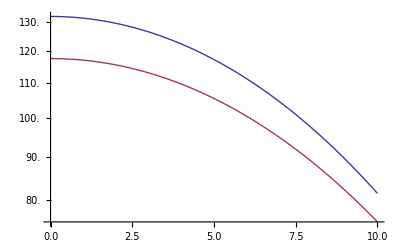

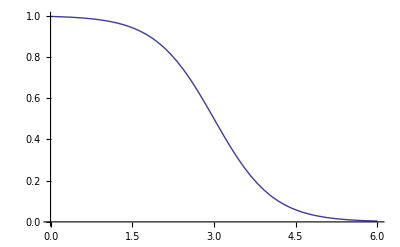

```mathematica
k=3;LogPlot[{ Abs[f[V,k,R,th Pi/180,15]]^2,Abs[Feik[V,k,R,th Pi/180]]^2},{th,0,10}]
```

```mathematica
Plot[1/(1+Exp[(r-3)/.54]),{r,0,6}]
```

-Graphics-

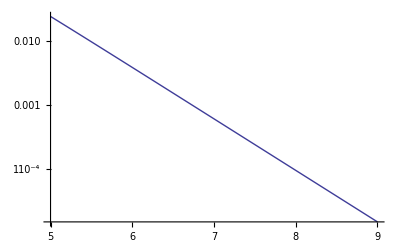

```mathematica
LogPlot[1/(1+Exp[(r-3)/.54]),{r,5,9}]
```

```mathematica
Exp[8.]
```

2980.96

```mathematica
Clear["Global`*"]
```

```mathematica
Clear[V,R];k/I Integrate[ b (Exp[-I V/k Sqrt[R^2-b^2]]-1),{b,0,R}]
```

```mathematica
-ⅈ k (-R^2/2+(k (-k+ⅇ^(-(ⅈ √(R^2) V)/k) (k+ⅈ √(R^2) V)))/V^2)/.{k->7,R->3,V->-1.9-.38I}
```

11.1596+5.67492 ⅈ

```mathematica
(Exp[-I V/k Sqrt[R^2-b^2]]-1)/.{k->3,b->.03,R->3,V->-1.9-.38I}
```

-1.22103+0.647171 ⅈ

```mathematica
-I V/k Sqrt[R^2-b^2]/.{k->3,R->3,b->.03}
```

-0.379981+1.8999 ⅈ

```mathematica
1/k Sqrt[R^2-b^2]/.{k->3,R->3,b->.03}
```

0.99995

```mathematica
1/k Sqrt[R^2-b^2]/.{k->3,R->3,b->.03}
```

0.917023

```mathematica
1/3Sqrt[3^2-0.03^2]
```

0.99995

```mathematica
k/I Integrate[ b (Exp[-I V/k Sqrt[R^2-b^2]]-1),{b,0,R}]
```

-ⅈ k (-R^2/2+(k (-k+ⅇ^(-(ⅈ √(R^2) V)/k) (k+ⅈ √(R^2) V)))/V^2)

```mathematica
-ⅈ k (-R^2/2+(k (-k+ⅇ^(-(ⅈ √(R^2) V)/k) (k+ⅈ √(R^2) V)))/V^2)/.V->(U+I W)
```

-ⅈ k (-R^2/2+(k (-k+ⅇ^(-(ⅈ √(R^2) (U+ⅈ W))/k) (k+ⅈ √(R^2) (U+ⅈ W))))/(U+ⅈ W)^2)

```mathematica
ComplexExpand[-ⅈ k (-R^2/2+(k (-k+ⅇ^(-(ⅈ √(R^2) (U+ⅈ W))/k) (k+ⅈ √(R^2) (U+ⅈ W))))/(U+ⅈ W)^2)]
```

(2 k^3 U W)/((U^2+W^2)^2)+(ⅇ^((√(R^2) W)/k) k^2 √(R^2) U^3 Cos[(√(R^2) U)/k])/((U^2+W^2)^2)-(2 ⅇ^((√(R^2) W)/k) k^3 U W Cos[(√(R^2) U)/k])/((U^2+W^2)^2)+(ⅇ^((√(R^2) W)/k) k^2 √(R^2) U W^2 Cos[(√(R^2) U)/k])/((U^2+W^2)^2)-(ⅇ^((√(R^2) W)/k) k^3 U^2 Sin[(√(R^2) U)/k])/((U^2+W^2)^2)-(ⅇ^((√(R^2) W)/k) k^2 √(R^2) U^2 W Sin[(√(R^2) U)/k])/((U^2+W^2)^2)+(ⅇ^((√(R^2) W)/k) k^3 W^2 Sin[(√(R^2) U)/k])/((U^2+W^2)^2)-(ⅇ^((√(R^2) W)/k) k^2 √(R^2) W^3 Sin[(√(R^2) U)/k])/((U^2+W^2)^2)+ⅈ ((k R^2)/2+(k^3 U^2)/((U^2+W^2)^2)-(k^3 W^2)/((U^2+W^2)^2)-(ⅇ^((√(R^2) W)/k) k^3 U^2 Cos[(√(R^2) U)/k])/((U^2+W^2)^2)-(ⅇ^((√(R^2) W)/k) k^2 √(R^2) U^2 W Cos[(√(R^2) U)/k])/((U^2+W^2)^2)+(ⅇ^((√(R^2) W)/k) k^3 W^2 Cos[(√(R^2) U)/k])/((U^2+W^2)^2)-(ⅇ^((√(R^2) W)/k) k^2 √(R^2) W^3 Cos[(√(R^2) U)/k])/((U^2+W^2)^2)-(ⅇ^((√(R^2) W)/k) k^2 √(R^2) U^3 Sin[(√(R^2) U)/k])/((U^2+W^2)^2)+(2 ⅇ^((√(R^2) W)/k) k^3 U W Sin[(√(R^2) U)/k])/((U^2+W^2)^2)-(ⅇ^((√(R^2) W)/k) k^2 √(R^2) U W^2 Sin[(√(R^2) U)/k])/((U^2+W^2)^2))

```mathematica
s=NDSolve[{-y''[x]+l(l+1)/x^2 y[x]+V/(1+Exp[(x-3)/aws])y[x]+9y[x]==0,y[0.0001]==0,y'[0.0001]==1},y,{x,0.0001,30}]
```

{{y→InterpolatingFunction[{{0.0001,30.}},<>]}}

```mathematica
y'[5]/y[5]/.s
```

{3.00351-0.00216502 ⅈ}

```mathematica
s=NDSolve[{-y''[x]+l(l+1)/x^2 y[x]+V/(1+Exp[(x-3)/aws])y[x]+9y[x]==0,y[0.0001]==0,y'[0.0001]==.5},y,{x,0.0001,30}]
```

{{y→InterpolatingFunction[{{0.0001,30.}},<>]}}

```mathematica
g=y'[5]/y[5]/.s
```

{3.00351-0.00216502 ⅈ}

```mathematica
g
```

{3.00351-0.00216502 ⅈ}

```mathematica
ct==(5 g j[l,k 5]-j[l,5k]- 5 k jp[l,5 k])/(5 g n[l,k 5]+n[l,5k]+5 k np[l,5 k])
```

ct=={1.03966-0.00516473 ⅈ}

```mathematica
tan phase shift for k=3,l=1
```

```mathematica
k=3;l=1;Do [s=NDSolve[{-y''[x]+l(l+1)/x^2 y[x]+V/(1+Exp[(x-3)/aws])y[x]-k^2y[x]==0,y[0.0001]==0,y'[0.0001]==.5},y,{x,0.0001,30}];g=y'[rm]/y[rm ]/.s;ct[rm_]:=(rm  g j[l,k rm]-j[l,rm k]- rm k jp[l,rm k])/(rm g n[l,k rm]-n[l,rm k]-rm k np[l,rm k]),{rm,5,10}]
```

```mathematica
ct[5]
```

{0.156182+0.176574 ⅈ}

```mathematica
ct[6]
```

{0.313143+0.189573 ⅈ}

```mathematica
Table[ct[rm],{rm,5,10}]
```

{{0.156182+0.176574 ⅈ},{0.313143+0.189573 ⅈ},{0.480837+0.213349 ⅈ},{0.66964+0.252642 ⅈ},{0.893505+0.317191 ⅈ},{1.17369+0.42762 ⅈ}}

```mathematica
V
```

-1.9-0.38 ⅈ

```mathematica
k=3;l=1;rm=5;s1=NDSolve[{-y''[x]+l(l+1)/x^2 y[x]+V/(1+Exp[(x-3)/aws])y[x]-k^2y[x]==0,y[0.0001]==0,y'[0.0001]==.05},y,{x,0.0001,30}]
```

{{y→InterpolatingFunction[{{0.0001,30.}},<>]}}

```mathematica
y[5]/.s1
```

{47.231-3.37108 ⅈ}

```mathematica
y'[5]/.s1
```

{-37.8241-23.2618 ⅈ}

```mathematica
{-37.824119656621676-23.26175850929885 ⅈ}/{47.23100867089812-3.3710804939007546 ⅈ}
```

{-0.761799-0.546883 ⅈ}

```mathematica
rm=5;g=y'[rm]/y[rm ]/.s1
```

{-0.761799-0.546883 ⅈ}

```mathematica
(rm  g j[l,k rm]-j[l,rm k]- rm k jp[l,rm k])/(rm g n[l,k rm]-n[l,rm k]-rm k np[l,rm k])
```

{1.16535+0.422889 ⅈ}

```mathematica
rm=6;g=y'[rm]/y[rm ]/.s1
```

{-0.314574-0.519913 ⅈ}

```mathematica
(rm  g j[l,k rm]-j[l,rm k]- rm k jp[l,rm k])/(rm g n[l,k rm]-n[l,rm k]-rm k np[l,rm k])
```

{1.17224+0.42678 ⅈ}

```mathematica
Agrees with numerical
```

```mathematica
rm
```

6

```mathematica
k=3;l=20;rm=8;s1=NDSolve[{-y''[x]+l(l+1)/x^2 y[x]+V/(1+Exp[(x-3)/aws])y[x]-k^2y[x]==0,y[0.0001]==0,y'[0.0001]==.05},y,{x,0.0001,20}]
```

{{y→InterpolatingFunction[{{0.0001,20.}},<>]}}

```mathematica
g=y'[rm]/y[rm ]/.s1;(rm  g j[l,k rm]-j[l,rm k]- rm k jp[l,rm k])/(rm g n[l,k rm]-n[l,rm k]-rm k np[l,rm k])
```

{0.000712987+0.000142754 ⅈ}

```mathematica
g=y'[rm]/y[rm ]/.s1;(rm  g j[l,k rm]-j[l,rm k]- rm k jp[l,rm k])/(rm g n[l,k rm]-n[l,rm k]-rm k np[l,rm k])
```

{0.195505+0.044088 ⅈ}

```mathematica
{0.9673226642225523+0.30594040198397054 ⅈ}
```

{0.967323+0.30594 ⅈ}

```mathematica
{1.0581474805845925+0.3553055940786558 ⅈ}
```

{1.05815+0.355306 ⅈ}

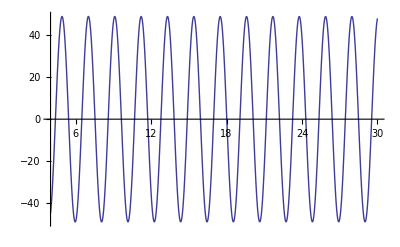

```mathematica
Plot[Evaluate[Re[y[x]]/.s1],{x,4,30}]
```

```mathematica
Clear[l]
```

```mathematica
k=3;rm=8;Do[s1=NDSolve[{-y''[x]+l(l+1)/x^2 y[x]+V/(1+Exp[(x-3)/aws])y[x]-k^2y[x]==0,y[0.0001]==0,y'[0.0001]==.05},y,{x,0.0001,20}];g[l_]:=y'[rm]/y[rm ]/.s1,{l,0,20}]
```

SetDelayed::write: Tag List in {-0.894757 - 0.000279312\ ⅈ}[l_] is Protected.

General::stop: Further output of SetDelayed :: write will be suppressed during this calculation.

```mathematica
ct[l]=(rm  g j[l,k rm]-j[l,rm k]- rm k jp[l,rm k])/(rm g n[l,k rm]-n[l,rm k]-rm k np[l,rm k]),{l=0,20}]
```

```mathematica
ct[1]
```

{((-1.89476-0.000279312 ⅈ) SphericalBesselJ[l,3]-3 (-1/6 SphericalBesselJ[l,3]+1/2 (SphericalBesselJ[-1+l,3]-SphericalBesselJ[1+l,3])))/((-1.89476-0.000279312 ⅈ) SphericalBesselY[l,3]-3 (-1/6 SphericalBesselY[l,3]+1/2 (SphericalBesselY[-1+l,3]-SphericalBesselY[1+l,3])))}